# Emergent Classicality

The goal is to explore how AI can extract and condense information about a qubit from local weak measurements in the environment that is entangled with the qubit. To demonstrate the idea that classical information is spread from the qubit into the environment and recollected by the intelligence to form emergent reality. Focus on how to quantify the relation between confidence and decoherence.

## Quantum Darwinism

### Measurement Theory

#### General Quantum Measurement

A quantum measurement is described by a set of Kraus operators K_a with the normalization condition

∑_a K_a^†K_a=𝟙.

Each possible index a labels a possible measurement outcome.

Let ρ be a density matrix of a quantum system. It evolves under the measurement as follows:

If unconditioned on the measurement outcome

ρ→∑_a K_a ρ K_a^†,

this will generally result in a mixed state density matrix.

If conditioned on the measurement outcome a

ρ→(K_a ρ K_a^†)/(Tr K_a ρ K_a^†),

and the outcome a appears with the probability

p_a=Tr K_a ρ K_a^†.

Pure state remains pure in this setup (conditioned on the outcome). Eq. (DisplayFormulaNumbered) defines a quantum trajectory of the state ρ.

#### Weak Measurement

Weak measurements are fussy (observer obtain very little information about the quantum system) and gentle (the perturbation to the quantum system is also very little). Krause operators of weak measurements are close to the identity.

For a single qubit, we can have the following schemes.

Binary measurement along a fixed axis

K_(±ϵ)=(σ^0±ϵ σ^z)/(√(2(1+ϵ^2))),

where ϵ controls the measurement strength. The measurement outcome is binary a=±ϵ. The normalization reads

∑_a K_a^†K_a=1/(2(1+ϵ^2))∑_(a=±ϵ) (σ^0+a σ^z)^2=σ^0.

Continuous measurement along any axis

K_ϵ=(σ^0+ϵ·σ)/(√(4π(1+ϵ^2))),

where |ϵ| controls the measurement strength. The measurement outcome is labeled by a three-component real vector ϵ. The normalization reads

∫ⅆϵ K_ϵ^†K_ϵ=1/(1+ϵ^2)∫ⅆϵ/(4π)(σ^0+ϵ·σ)^2=σ^0,

where the integral measure is defined such that ∫ⅆϵ/(4π)=1 (like spherical angle).

#### Quantum Trajectory

Consider a single qubit, its density matrix ρ is universally parameterized by a three-component real vector n (no necessarily unit vector if ρ can be mixed),

ρ=(σ^0+n·σ)/2.

##### Binary Measurement

Conditioned on the outcome a=±ϵ, the n vector evolves as

n_1→((1-a^2)n_1)/(1+2a n_3+a^2),
n_2→((1-a^2)n_2)/(1+2a n_3+a^2),
n_3→((1+a^2)n_3+2a)/(1+2a n_3+a^2),

```mathematica
Collect[(σ[0]+a σ[3])·(σ[0]+n1 σ[1]+n2 σ[2]+n3 σ[3])·(σ[0]+a σ[3]),_σ]
```

(1+a^2+2 a n3) σ[0]+(n1-a^2 n1) σ[1]+(n2-a^2 n2) σ[2]+(2 a+n3+a^2 n3) σ[3]

Details.

with probability

p_(a=±ϵ)=(1+2a n_3+a^2)/(2(1+a^2)).

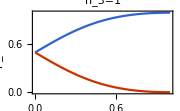

```mathematica
Block[{n3=1},
Plot[Evaluate[(1+2 n3{1,-1}ϵ+ϵ^2)/(2(1+ϵ^2))],{ϵ,0,1},FrameLabel->{"ϵ","\!\(p\_±ϵ\)"},PlotLabel->StringTemplate["\!\(n\_3=`1`\)"][n3],PlotRange->{0,1},PlotRangePadding->Scaled[.05],ImageSize->180]]
```

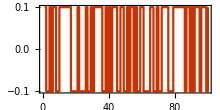
-Graphics3D--Graphics-

```mathematica
Block[{ϵ=0.1,measure,ns,os},
measure[{n1_,n2_,n3_}]:=Block[{ps,a,n},
ps=(1+2ϵ n3{1,-1}+ϵ^2)/(2(1+ϵ^2));
Sow[a=RandomChoice[ps->{ϵ,-ϵ}]];
{(1-a^2)n1,(1-a^2)n2,(1+a^2)n3+2 a}/(1+2 a n3+a^2)];
{ns,{os}}=Reap[NestList[measure,{1,0,0},100]];
Row@{Graphics3D[{First@ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Opacity[0.1],White],MeshStyle->Opacity[0.1]],Point[ns]},Boxed->False,ImageSize->160],
ListLinePlot[os,PlotStyle->Red,FrameLabel->{"step","outcome"},AspectRatio->1/2,InterpolationOrder->0,ImageSize->220]}]
```

The state ρ will be attracted towards the north/south pole while doing random walk along the path. The outcome will gradually become biased by ϵ amount.

##### Continuous Measurement

Conditioned on the outcome ϵ, the n vector evolves as

n→(n(1-ϵ^2)+2ϵ(1+ϵ·n))/(1+2ϵ·n+ϵ^2),

```mathematica
Collect[(σ[0]+ϵ1 σ[1]+ϵ2 σ[2]+ϵ3 σ[3])·(σ[0]+n1 σ[1]+n2 σ[2]+n3 σ[3])·(σ[0]+ϵ1 σ[1]+ϵ2 σ[2]+ϵ3 σ[3]),_σ]
```

(1+2 n1 ϵ1+ϵ1^2+2 n2 ϵ2+ϵ2^2+2 n3 ϵ3+ϵ3^2) σ[0]+(n1+2 ϵ1+n1 ϵ1^2+2 n2 ϵ1 ϵ2-n1 ϵ2^2+2 n3 ϵ1 ϵ3-n1 ϵ3^2) σ[1]+(n2-n2 ϵ1^2+2 ϵ2+2 n1 ϵ1 ϵ2+n2 ϵ2^2+2 n3 ϵ2 ϵ3-n2 ϵ3^2) σ[2]+(n3-n3 ϵ1^2-n3 ϵ2^2+2 ϵ3+2 n1 ϵ1 ϵ3+2 n2 ϵ2 ϵ3+n3 ϵ3^2) σ[3]

Details.

with probability density (upon fixed |ϵ|)

p(ϵ)ⅆϵ=(1+2ϵ·n+ϵ^2)/(4π(1+ϵ^2))ⅆϵ.

In fact, the continuous measurement scheme is equivalent to the binary measurement with a random axis isotropically sampled on the sphere.

To generate random ϵ given n, we can choose to represent ϵ in spherical coordinate with respect to n (as the direction toward the north pole). Let θ be the angle between ϵ and n (i.e. ϵ·n=ϵ n cos θ), Eq. (DisplayFormulaNumbered) induces a distribution of θ

p(θ)ⅆθ=2π sin θⅆθ(1+2ϵ·n+ϵ^2)/(4π(1+ϵ^2))=((1+2 ϵ n cos θ+ϵ^2)sin θ)/(2(1+ϵ^2))ⅆθ,

where ϵ=|ϵ| and n=|n| are the lengths of the vectors. From the probability distribution function p(θ), we can define the cumulative distribution function

x(θ)=∫_0^θ p(θ)ⅆθ=((1+2n ϵ cos^2 θ/2+ϵ^2)sin^2 θ/2)/(1+ϵ^2).

```mathematica
Integrate[(1+2 n ϵ Cos[θ]+ϵ^2)Sin[θ]/(2(1+ϵ^2)),{θ,0,θ}]
```

((1+n ϵ+ϵ^2+n ϵ Cos[θ]) Sin[θ/2]^2)/(1+ϵ^2)

Details.

Its inverse function reads

θ(x)=2 arctan √((2+y)/(2-y)),
y=(1+ϵ^2-√((1+2n ϵ+ϵ^2)^2-8n ϵ (1+ϵ^2)x))/(n ϵ).

```mathematica
Last@Solve[(1+2 n ϵ Cos[θ/2]^2+ϵ^2)Sin[θ/2]^2/(1+ϵ^2)==x,θ]
```

{θ→ConditionalExpression[2 (ArcTan[1/2 √(2-1/(n ϵ)-ϵ/n+(√((-1-2 n ϵ-ϵ^2)^2-8 n ϵ (x+x ϵ^2)))/(n ϵ)),1/2 √(2+1/(n ϵ)+ϵ/n-(√((-1-2 n ϵ-ϵ^2)^2-8 n ϵ (x+x ϵ^2)))/(n ϵ))]+2 π C[1]),C[1]∈ℤ]}

Details.

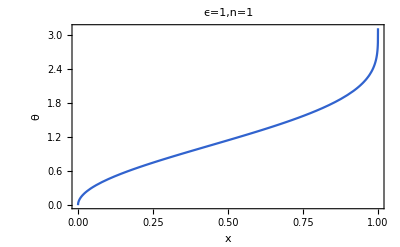

```mathematica
Block[{ϵ=1,n=1},
Plot[Block[{y},y=(1+ϵ^2-Sqrt[(1+2n ϵ+ϵ^2)^2-8n ϵ(1+ϵ^2)x])/(n ϵ);
2ArcTan[Sqrt[(2+y)/(2-y)]]],{x,0,1},FrameLabel->{"\!\(x\)","\!\(θ\)"},PlotLabel->StringTemplate["\!\(ϵ=`1`,n=`2`\)"][ϵ,n]]]
```

With this, we can first sample x from a uniform distribution in [0,1] (i.e. p(x)=1), then deform x to θ by Eq. (DisplayFormulaNumbered), the obtained θ will follow the desired distribution p(θ), because the probability is deformed by p(x)(∂x)/(∂θ)=p(θ). As we sample the angle θ, we can then uniformly sample ϕ from [0,2π), then the spherical coordinate (θ,ϕ) specifies ϵ with respect to n.

```mathematica
Block[{ϵ=0.05,measure,ns,ϵs,sphere},
measure[n:{_,_,_}]:=Block[{frame,θ,ϕ,m},
frame=RotationMatrix[{n,{0,0,1}}];
θ=Block[{nn=Norm[n],x=RandomReal[{0,1}],y},y=(1+ϵ^2-Sqrt[(1+2nn ϵ+ϵ^2)^2-8nn ϵ(1+ϵ^2)x])/(nn ϵ);
2ArcTan[Sqrt[(2+y)/(2-y)]]];
ϕ=RandomReal[{0,2π}];
Sow[m=ϵ{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}.frame];
(n(1-m.m)+2m(1+m.n))/(1+2m.n+m.m)];
{ns,{ϵs}}=Reap[NestList[measure,{0,0,1},100]];
sphere=First@ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Opacity[0.1],White],MeshStyle->Opacity[0.1]];
Row@{Graphics3D[{sphere,Point[ns]},Boxed->False,PlotLabel->Style["state",14,Black],ImageSize->160],Graphics3D[{sphere,Red,Point[ϵs/ϵ]},Boxed->False,PlotLabel->Style["outcome",14,Black],ImageSize->160]}
]
```

-Graphics3D--Graphics3D-

The state will diffuse around its initial position. The outcome is roughly biased by ϵ amount.

### GHZ State

#### Local Measurement

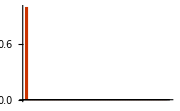
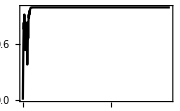
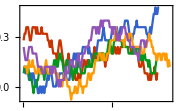

```mathematica
Block[{L=6,ϵ=0.1,Id,S,ρ0,measure,ρs,ϵs},
Id=SparseArray[{Band[{1,1}]->1},{2^L,2^L}];
S=SparseArray@Represent[Table[σ@@SparseArray[{i->a},L],{i,L},{a,3}]];
ρ0=#⊗#/2&@SparseArray[{1->1,-1->1},{2^L}];
measure[ρ1_]:=Block[{i,m,M,ρ2,p,a},
i=RandomInteger[{2,L}];
m={0,0,1};
M=AssociationThread[{1,-1}->{Id+ϵ #,Id-ϵ #}/Sqrt[2(1+ϵ^2)]]&[m.S⟦i⟧];
ρ2=#.ρ1.ConjugateTranspose[#]&/@M;
p=Re[Tr/@ρ2];
a=RandomChoice[p/@{1,-1}->{1,-1}];
Sow[a m,i];
ρ2[a]/p[a]];
{ρs,ϵs}=Reap[NestList[measure,ρ0,1000],Range[2,L]];
{BarChart[Re@Normal@Diagonal[Last@ρs],ImageSize->180],ListLinePlot[Re[Tr[S⟦1,3⟧.#]&/@ρs],PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[MovingAverage[#,50]&/@ϵs⟦All,1,All,3⟧,PlotRange->All,ImageSize->180]}
]
```

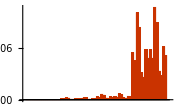
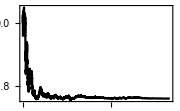
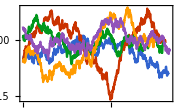

```mathematica
Block[{L=6,ϵ=0.05,Id,S,ρ0,measure,ρs,ϵs},
Id=SparseArray[{Band[{1,1}]->1},{2^L,2^L}];
S=SparseArray@Represent[Table[σ@@SparseArray[{i->a},L],{i,L},{a,3}]];
ρ0=#⊗#/2&@SparseArray[{1->1,-1->1},{2^L}];
measure[ρ1_]:=Block[{i,m,M,ρ2,p,a},
i=RandomInteger[{2,L}];
m=Normalize@RandomVariate[NormalDistribution[],{3}];
M=AssociationThread[{1,-1}->{Id+ϵ #,Id-ϵ #}/Sqrt[2(1+ϵ^2)]]&[m.S⟦i⟧];
ρ2=#.ρ1.ConjugateTranspose[#]&/@M;
p=Re[Tr/@ρ2];
a=RandomChoice[p/@{1,-1}->{1,-1}];
Sow[a m,i];
ρ2[a]/p[a]];
{ρs,ϵs}=Reap[NestList[measure,ρ0,5000],Range[2,L]];
{BarChart[Re@Normal@Diagonal[Last@ρs],ImageSize->180],ListLinePlot[Re[Tr[S⟦1,3⟧.#]&/@ρs],PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[MovingAverage[#,200]&/@ϵs⟦All,1,All,3⟧,PlotRange->All,ImageSize->180]}
]
```

#### Mutual Information

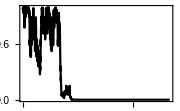
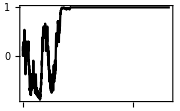
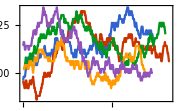
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Block[{L=6,ϵ=0.05,Id,S,ρ0,measure,MI,ρs,ϵs},
Id=SparseArray[{Band[{1,1}]->1},{2^L,2^L}];
S=SparseArray@Represent[Table[σ@@SparseArray[{i->a},L],{i,L},{a,3}]];
ρ0=#⊗#/2&@SparseArray[{1->1,-1->1},{2^L}];
measure[ρ1_]:=Block[{i,m,M,ρ2,p,a},
i=RandomInteger[{2,L}];
m={0,0,1};
(*m=Normalize@RandomVariate[NormalDistribution[],{3}];*)
M=AssociationThread[{1,-1}->{Id+ϵ #,Id-ϵ #}/Sqrt[2(1+ϵ^2)]]&[m.S⟦i⟧];
ρ2=#.ρ1.ConjugateTranspose[#]&/@M;
p=Re[Tr/@ρ2];
a=RandomChoice[p/@{1,-1}->{1,-1}];
Sow[a m,i];
ρ2[a]/p[a]];
MI[ρ_]:=Block[{ρr,Ent},
ρr=TensorContract[ArrayReshape[ρ,ConstantArray[2,2L]],Table[{i,i+L},{i,3,L}]];
Ent[ps_]:=Re@Total[If[#==0.,0.,-# Log[2,#]]&/@ps];
Ent[Eigenvalues@N@TensorContract[ρr,{{2,4}}]]+Ent[Eigenvalues@N@TensorContract[ρr,{{1,3}}]]-Ent[Eigenvalues@N@ArrayReshape[ρr,{4,4}]]];
{ρs,ϵs}=Reap[NestList[measure,ρ0,2000],Range[2,L]];
{BarChart[Re@Normal@Diagonal[Last@ρs],ImageSize->180],ListLinePlot[MI/@ρs,PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[Re[Tr[S⟦1,3⟧.#]&/@ρs],PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[MovingAverage[#,100]&/@ϵs⟦All,1,All,3⟧,PlotRange->All,ImageSize->180]}
]
```

We can consider a generative model like RBM

E({v},{h})=∑_(i,j) w_ij v_i h_j+∑_j b_j h_j.

How many mode h do we need? → dimension of Hilbert space of the system.

How confident we can determine {h} based on {v}

p({h}|{v})=(p({v}|{h})p({h}))/(p({v}))

Also this is not calculated simply by clamping a specific {v}, because we could have already collect a bunch of data about {v}. Different configurations of {v} have appeared many times. We want to evaluate this based on the entire data. To this end, we need to first figure out how to evaluate this Bayesian probability give a set of {v} configurations jointly.

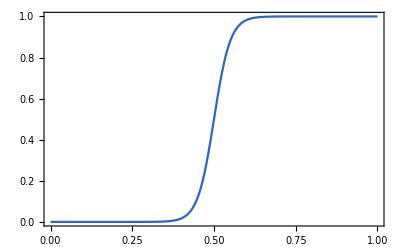

```mathematica
Plot[Block[{q=1-p,n=10},p^n/(p^n+q^n)],{p,0,1}]
```

We first train the machine on long-time data, where the state has already collapsed. This is to teach the machine about how to use the apparatus, how to read out useful information. After that we can apply the same machine to analyze the data starting from the GHZ state. At the beginning the local measurement looks like 1:1 random, because the reduced density matrix is identity, then no knowledge can be learned. As weak measurement goes information about the qubit is gradually obtained, we use the trained machine (generative model) to evaluate the confidence of the internal state {h} to investigate how this confidence raises as the decoherence happens. (Without training, the state still decohere but no knowledge is gained by the machine.)

To work with local measurement, we need a generative model that can marginalize easily.

We can also consider to remove the locality condition, then the observer should be able to develop a full understanding of the entire quantum state (capturing non-local correlations).

#### Joint Distribution

We do not need to sample the weak measurement outcome one-by-one. We can sample a sequence of outcomes all at once from their joint distribution.

We will consider the binary measurement on GHZ state.

K_±=e^(±ϵ Z/2)/(√(2cosh ϵ))=1/(√(2 cosh ϵ))(e^(±ϵ/2) | 0
0 | e^(∓ϵ/2)).

One can verify that ∑_a K_a^†K_a=𝟙.

Suppose we take totally n weak measurements, among which n_± outcomes are ±. This means the overall measurement operator (in the space spanned by the all-up and all-down states) is

K=K_+^(n_+)K_-^(n_-)=1/(2 cosh ϵ)^(n/2)(e^(ϵ/2(n_+-n_-)) | 0
0 | e^(-ϵ/2(n_+-n_-))).

The GHZ state in this subspace is represented as

Ψ=1/(√(2cosh α))(e^(α/2)
e^(-α/2))

We can calculate the probability for this to happen

p(n_+,n_-)=Ψ K^†KΨ
=(cosh(ϵ(n_+-n_-)+α))/(2cosh α (2 cosh ϵ)^n).

Introduce the magnetization -1≤m≤1,

{ | n_++n_-=n
n_+-n_-=m n⇒{ | n_+=(1+m)n/2
n_-=(1-m)n/2

The probability for the weak measurement outcome sequence to have a particular magnetization m is

p(m)=(n
(1+m)n/2)(cosh(ϵ m n+α))/(2cosh α (2 cosh ϵ)^n).

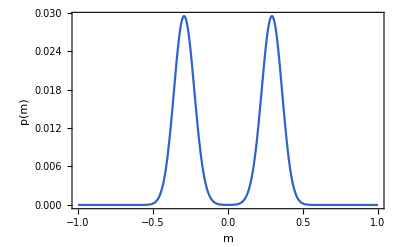

```mathematica
Block[{α=0,ϵ=0.3,n=200},
Plot[{2 Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2]},{m,-1,1},FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->All]]
```

The weak measurement outcome will develop the two-peak structure for large enough total sample number n.

The splitting happens when ∂_m^2 p(m) changes sign, which happens when

∂_m^2 p(m)=n^2/(2(2 cosh ϵ)^n)(n
n/2)(2 ϵ^2-ψ^(1)(1+n/2))=0,

```mathematica
FullSimplify[D[2 Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,2}]/.m->0]
```

1/2 n^2 Binomial[n,n/2] (2 ϵ^2-PolyGamma[1,1+n/2]) (Csch[ϵ] Sinh[2 ϵ])^-n

Details.

where ψ^(1) is the polygamma function. The solution of Eq. (DisplayFormulaNumbered) is given by

ϵ=(1/2 ψ^(1)(1+n/2))^(1/2)→^(n→∞)n^(-1/2).

```mathematica
Series[Sqrt[PolyGamma[1,1+n/2]/2],{n,∞,1}]
```

√(1/n)+O[1/n]^(3/2)

Details.

After the weak measurement, the GHZ state becomes

KΨ=1/(2 cosh ϵ)^(n/2)1/(√(2cosh α))(e^((ϵ m n+α)/2)
e^(-(ϵ m n+α)/2)),

So the quantum coherence is given by

c(m)=1/(cosh(ϵ m n+α)).

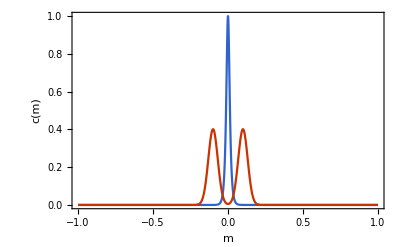

```mathematica
Block[{α=0,ϵ=0.1,n=1000},
Plot[{Sech[ϵ m n+α],Exp[Log[2 Cosh[ϵ m n+α]]-n Log[2 Cosh[ϵ]]-Log[2Cosh[α]]+LogGamma[n+1.]-LogGamma[(1+m)n/2+1.]-LogGamma[(1-m)n/2+1.]+Log[n]/2]},{m,-1,1},FrameLabel->{"\!\(m\)","\!\(c(m)\)"},PlotRange->All]]
```

We also plot p(m) in red to show that most likely the state has already decohere when the two modes split apart. We can try to quantify the confidence of the classification.

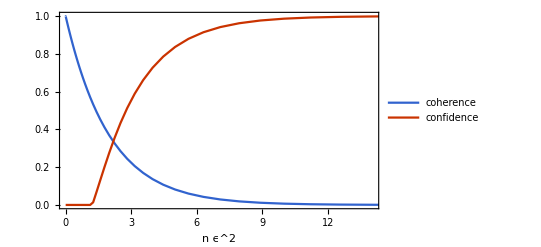

```mathematica
Block[{α=0,ϵ=0.01},ListLinePlot[Thread[Table[Block[{n ,p,c},
n=10^lgn/ϵ^2;
p[m_]:=Exp[Log[2 Cosh[ϵ m n+α]]-n Log[2 Cosh[ϵ]]-Log[2Cosh[α]]+LogGamma[n+1.]-LogGamma[(1+m)n/2+1.]-LogGamma[(1-m)n/2+1.]+Log[n/2]];
c=
NIntegrate[Exp[Log[n]-n Log[2 Cosh[ϵ]]-Log[2Cosh[α]]+LogGamma[n+1.]-LogGamma[(1+m)n/2+1.]-LogGamma[(1-m)n/2+1.]],{m,-1,1}];
{n ϵ^2,#}&/@{c,1-Clip[p[0]/p[ϵ],{0,1}]}],{lgn,-3,1.5,0.05}]],FrameLabel->{"\!\(n ϵ\^2\)"},PlotLegends->{"coherence","confidence"}]]
```

Universal curves emerge in the weak measurement limit as ϵ→0.

```mathematica
Block[{n=200},
Graphics3D[{AbsolutePointSize[3],Point[{#,0.5#,0.2#}&/@(RandomVariate[NormalDistribution[0,0.15],{n}]+0.5RandomChoice[{1,-1},{n}])+RandomVariate[NormalDistribution[0,0.02],{n,3}]],
{Dashed,Red,Line[{1,0.5,0.2}#&/@{-1,1}]}},PlotRange->1]]
```

-Graphics3D-

## Quantum State Tomography

### VAE Model

#### Density Matrix Model

Define the single-qubit POVM

E_m=(σ^0+m·σ)/2.

We have

Tr E_m=1, Tr E_m E_m'=(1+m·m')/2.

Consider the many-body density matrix to be modeled by

ρ=∫⊗_i E_(m_i(z))p(z)ⅆz,
=∫E[m]p[m]ⅅ[m],

where z is the set of latent variables and m_i(z) are functions of z. The prior distribution p(z) is taken to be normalized Gaussian, such that all the non-triviality goes to the mapping m_i(z).

The key difference from Juan’s setup: they tries to build a generative model to directly model the measurement outcome distribution and then recover the density matrix of the outcome distribution. But we do not have an explicit model for measurement outcome (although we can estimate the outcome probability base on our model), we directly model the density matrix.

In this way, we achieve three advantages:

To recover density matrix from outcome distribution, a non-singular overlapping matrix T between the POVM’s is needed. This restricts the choice of POVM. In particular, we can only work with discrete POVM which forbidden us from applying differentiable generative models (flow-based, VAE ...). Our scheme can work with continuous POVMs and enables the application of differentiable generative model.

In principle, Juan’s framework can also be generalized to weak measurement, but as the measurement becomes weaker, the overlapping matrix T becomes more singular, and the algorithm is very unstable. We do not model the outcome distribution but directly model the density matrix, which is more stable in the weak measurement limit.

Boltzmann machine and autoregressive models are hard to marginalize. It turns out that VAE is easy to marginalize, which allows quantum state tomography from local measurements and density matrix reconstruction.

#### Weak Measurement

The weak measurement at site i will obtain outcome x with probability

p_mdl(x)=Tr E_x ρ
=∫(1+x·m_i(z))/2 p(z)ⅆz
=∫p(x|z)p(z)ⅆz,

where p(x|z)=(1+x·m_i(z))/2. So the measurement outcome probability nicely fit in the framework of classical probability theory. As the prior distribution p(z) is always assumed to be normal Gaussian, all the non-triviality enters from the conditional distribution p(x|z) which eventually relies on a non-trivial mapping of m_i(z). We relies on neural network to realize the non-linear map m_i(z) with broad enough representation power.

#### Training Objectives

The original objective is to maximize the likelihood on observed outcomes

max ℒ:ℒ=ln p_mdl(x).

However, evaluating p_mdl(x) involves sampling over z\[Distributed]p(z), which is inefficient. The idea of VAE is to build a variational ansatz q(z|x) to approximate p(z|x), which allows us to do importance sampling of z\[Distributed]q(z|x) by inference. Now the objective becomes two folded:

to maximize likelihood ln p(x),

and to bring q(z|x) close to p(z|x) by minimizing their KL divergence.

So the objective function can be chosen as

ℒ=𝔼_(z\[Distributed]q(z|x))ln p(x)-D_KL(q(z|x)||p(z|x))
=𝔼_(z\[Distributed]q(z|x))(ln p(x)+ln p(z|x)-ln q(z|x))
=𝔼_(z\[Distributed]q(z|x))(ln p(z)+ln p(x|z)-ln q(z|x))
=𝔼_(z\[Distributed]q(z|x))ln p(x|z)-D_KL(q(z|x)||p(z)).

### Density Matrix Modeling

#### Tetra POVM

##### On-Site Case

Consider a the tetra basis of qubit POVM,

E_x=K_x^†K_x=1/4(σ^0+x·σ),

where x=x m labels the POVM and m is a unit vector taken from

m=(1,1,1)/(√3),(1,-1,-1)/(√3),(-1,1,-1)/(√3),(-1,-1,1)/(√3).

It can be verified that

∑_x E_x=σ^0.

The overlap matrix reads

T_(x_1 x_2)=Tr(E_x_1 E_x_2^†)=1/8-(x_1 x_2)/24(1-4 δ_(x_1 x_2)),

```mathematica
Block[{ms,Es,T},
ms=Normalize/@{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
Es[x_]:=Represent[(σ[0]+#.(σ/@Range[3]))/4]&/@(x ms);
T=FullSimplify[Table[Tr[E1.ConjugateTranspose[E2]],{E1,Es[x1]},{E2,Es[x2]}],x1>0&&x2>0];
MatrixForm@Expand@T]
```

(1/8+(x1 x2)/8 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24
1/8-(x1 x2)/24 | 1/8+(x1 x2)/8 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24
1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8+(x1 x2)/8 | 1/8-(x1 x2)/24
1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8+(x1 x2)/8)

Details.

where x_(1,2)=|x_(1,2)| denotes the norm of the vectors. Its inverse gives the metric

(T^-1)_(x_1 x_2)=1/2-3/(2 x_1 x_2)(1-4 δ_(ϵ_1 ϵ_2)).

```mathematica
Block[{ms,Es,T},
ms=Normalize/@{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
Es[x_]:=Represent[(σ[0]+#.(σ/@Range[3]))/4]&/@(x ms);
T=FullSimplify[Table[Tr[E1.ConjugateTranspose[E2]],{E1,Es[x1]},{E2,Es[x2]}],x1>0&&x2>0];
MatrixForm@Simplify@Inverse@T]
```

(1/2+9/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2)
1/2-3/(2 x1 x2) | 1/2+9/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2)
1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2+9/(2 x1 x2) | 1/2-3/(2 x1 x2)
1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2+9/(2 x1 x2))

Details.

Special case: when x_1=x_2=1,

T_(x_1 x_2)=1/8-(1-4 δ_(x_1 x_2))/24=Piecewise[{{1/4, if x_1=x_2,}, {1/12, if x_1≠x_2.}}]

(T^-1)_(x_1 x_2)=1/2-(3(1-4 δ_(x_1 x_2)))/2=Piecewise[{{5, if x_1=x_2,}, {-1, if x_1≠x_2.}}]

In general T^-1 becomes singular when either x_1 or x_2 approaches zero.

We can use T^-1 to construct a tetra IOVM

(Ẽ)_x=∑_x' (T^-1)_(x x')E_x'
=1/2(σ^0+3/x^2 x·σ),

```mathematica
Block[{ms,Es,T,invT},
ms=Normalize/@{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
Es[x_]:=Represent[(σ[0]+#.(σ/@Range[3]))/4]&/@(x ms);
T=FullSimplify[Table[Tr[E1.ConjugateTranspose[E2]],{E1,Es[x]},{E2,Es[xp]}],x>0&&xp>0];
invT=Simplify@Inverse@T;
Simplify[Abstract/@(invT.Es[xp])]]
```

{(x σ[0]+√3 (σ[1]+σ[2]+σ[3]))/(2 x),(x σ[0]+√3 (σ[1]-σ[2]-σ[3]))/(2 x),(x σ[0]-√3 (σ[1]-σ[2]+σ[3]))/(2 x),(x σ[0]-√3 (σ[1]+σ[2]-σ[3]))/(2 x)}

Details.

where x=|x| is the norm of x vector and the result is independent of the norm of the x' vector that has been summed over in Eq. (DisplayFormulaNumbered). In the case that x=m as a unit vector, such that E_m is the standard tetra POVM, the corresponding tetra IOVM reads

(Ẽ)_m=1/2(σ^0+3m·σ),

where m are unit vectors taken from Eq. (DisplayFormulaNumbered).

##### Many-Body Case

We define multi-qubit POVM as a product of single-qubit POVM

E[m]=∏_i E_m_i=∏_i 1/4(σ^0+m_i·σ).

This defines the metric

T[m,m']=Tr (E[m]E[m']^†)=∏_i T_(m_i m'_i),

and its inverse

T^-1[m,m']=∏_i (T^-1)_(m_i m'_i).

Given the probability of measurement outcome

p[m]=Tr E[m]ρ,

the density matrix can be back out from the outcome probability by

ρ=∑_([m][m']) E[m]^†T^-1[m,m']p[m'].

Because

∑_([m'][m'']) Tr (E[m]E[m']^†)T^-1[m',m'']p[m'']
=∑_([m'][m'']) T[m,m']T^-1[m',m'']p[m'']
=p[m].

However, this approach has a few problem

For weak measurement, T^-1 will be come singular, if p[m] is considered to be the weak measurement probability.

m must be discrete, measurement are restricted to be performed along special axis,

It is difficult to marginalize p[m] for local measurement (this is not a problem of the formulation but a problem of the choice of generative model).

#### Dual IOVM

In Eq. (DisplayFormulaNumbered), we can absorb T^-1 (sign structure) to E^† and define the dual IOVM

Ẽ[m]=∑_[m'] E[m']^†T^-1[m',m].

In fact, Ẽ[m] can be defined even if T^-1 does not exist. It is defined through the isometry relation that (the summation of [m] can be generalized to integration for the continuous case)

∑_[m] Ẽ[m]⊗E[m]==.

Then we can show that

ρ=∑_[m] Ẽ[m]Tr(E[m]ρ)=∑_[m] Ẽ[m]p[m],

where p[m] is the measurement outcome probability which is positive definite. For generic measurement M[x],

p[x]=Tr M[x]ρ=∑_[m] Tr (M[x]Ẽ[m])p[m]=∑_[m] p[x|m]p[m],

where the conditional distribution is given by

p[x|m]=Tr (M[x]Ẽ[m]).

Although  p[x|m] is not positive for all possible outcomes x, but as long as the measurement is weak enough, the positivity can be bounded.

```mathematica
Abstract/@tTr[{PauliMatrix/@Range[0,3],ArrayReshape[Inverse@ArrayReshape[Sum[If[a==0,1,1/3]PauliMatrix[a]⊗PauliMatrix[a],{a,0,3}],{4,4}],{2,2,2,2}]},{{2,5},{3,4}}]
```

{σ[0]/2,(3 σ[1])/2,(3 σ[2])/2,(3 σ[3])/2}

#### Spherical POVM

##### Single-Qubit Case

Define the single-qubit POVM (assuming m is unit vector)

E_m=(σ^0+m·σ)/2.

The corresponding dual IOVM is given by

(Ẽ)_m=σ^0+3m·σ.

We have

trace properties

Tr E_m=1, Tr E_m E_m'=(1+m·m')/2,

isometry (assuming ∫_(S^2) ⅆm =1)

∫_(S^2) ⅆm (Ẽ)_m⊗E_m
=1/2∫_(S^2) ⅆm (σ^0+3m·σ)⊗(σ^0+m·σ)
=1/2∫_(S^2) ⅆm (σ^0+3 m_1 σ^1+3 m_2 σ^2+3 m_3 σ^3)⊗(σ^0+m_1 σ^1+m_2 σ^2+m_3 σ^3)
=1/2(σ^00+σ^11+σ^22+σ^33).

```mathematica
Integrate[x^2,{x,y,z}∈Sphere[]]/(4π)
```

1/3

Details.

Therefore

∫_(S^2) ⅆm (Ẽ)_m⊗E_m=(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)=swap

```mathematica
Represent[σ[0,0]+σ[1,1]-σ[2,2]+σ[3,3]]//MatrixForm
```

(2 | 0 | 0 | 2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
2 | 0 | 0 | 2)

Details.

Therefore we can establish a model for the density matrix

ρ=∫_(S^2) ⅆm (Ẽ)_m Tr(E_m ρ)=∫_(S^2) ⅆm (Ẽ)_m p_m,

where p_m=Tr(E_m ρ) is positive definite and can be model by any generative model.

##### Multi-Qubit Case

For multiple sites, we define

the POVM and its dual

E[m]=∏_i E_m_i=∏_i (1+m_i·σ_i)/2,
Ẽ[m]=∏_i (Ẽ)_m_i=∏_i (1+3m·σ).

They satisfies the isometry relation

∫ⅅ[m]Ẽ[m]⊗E[m]=SWAP.

the measurement operator (overs non-local observables)

M[x]=1/2(1+∑_[μ] x_[μ]σ^[μ]).

Eq. (DisplayFormulaNumbered) implies that the density matrix can be modeled by

ρ=∫ⅅ[m]Ẽ[m]p[m],

with p[m]=Tr E[m]ρ positive definite. We introduce latent variable z to model p[m]=∫ⅆz δ[m-m(z)]p(z), such that

ρ=∫ⅆzẼ[m(z)]p(z).

Based on this model, the weak measurement outcome should follow

p(x)=Tr M[x]ρ=∫ⅆz p(x|z)p(z),

where the conditional distribution is given by

p(x|z)=Tr M[x]Ẽ[m(z)]=

## Emergent Classical Reality

### Quantum World

#### Model Setup

Consider a model of quantum circuit coupled to neural network via weak measurement interface. Question: can artificial intelligence extract a strong measurement outcome from the weak measurement signals on the ancilla qubits.

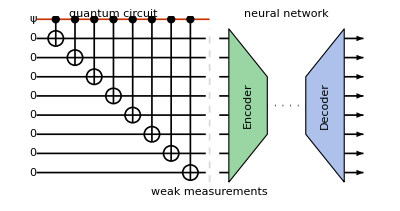

```mathematica
Block[{a=0.4,b=0.3,g=0.2,L=8,t=1},
Graphics[{AbsoluteThickness[1.2],
{Red,Line[{{0,0},{L+1,0}}]},
Table[{
{Line[{{0,y},{L+1-g,y}}]},
{EdgeForm[AbsoluteThickness[1.2]],White,Disk[{L+1+g,y},b,{-π/2,π/2}]},Line[{{L+1+g+b,y},{L+1+t,y}}],Arrow[{{L+1+7t,y},{L+1+8t,y}}]},{y,-L,-1}],
{Dotted,Line[{{L+1+3t,-(L+1)/2},{L+1+5t,-(L+1)/2}}]},Translate[{{Lighter[Green,0.6],EdgeForm[Black],Polygon[{{-t,-L/2},{-t,L/2},{t,1.5},{t,-1.5}}]},{Text["Encoder",{0,0},{0,0},{0,1}]}},{L+1+2t,-(L+1)/2}],
Translate[{{Lighter[Blue,0.6],EdgeForm[Black],Polygon[{{t,-L/2},{t,L/2},{-t,1.5},{-t,-1.5}}]},{Text["Decoder",{0,0},{0,0},{0,1}]}},{L+1+6t,-(L+1)/2}],
AbsolutePointSize[6],Table[{Point[{x,0}],Line[{{x,0},{x,-x-a}}],Circle[{x,-x},a]},{x,1,L}],
Text["\!\(ψ\)",{0,0},{1.2,0}],
Table[Text["\!\(0\)",{0,y},{1.2,0}],{y,-1,-L,-1}],
Text["quantum circuit",{L/2,0},{0,-1}],Text["neural network",{L+1+4t,0},{0,-1}],
{Dashed,LightGray,Line[{{L+1,-L-0.5},{L+1,-0.5}}]},
Text["weak measurements",{L+1,-L-1}]},ImageSize->{Automatic,150}]]
```

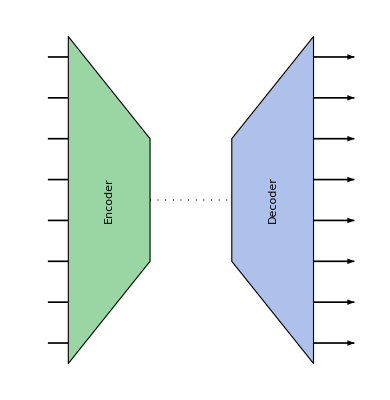

```mathematica
Block[{a=0.4,b=0.3,g=0.2,L=8,t=1},
Graphics[{AbsoluteThickness[1.2],Arrowheads[0.08],
Table[{
{EdgeForm[AbsoluteThickness[1.2]],White,Disk[{L+1+g,y},b,{-π/2,π/2}]},Line[{{L+1+g+b,y},{L+1+t,y}}],Arrow[{{L+1+7t,y},{L+1+8t,y}}]},{y,-L,-1}],
{Dotted,Line[{{L+1+3t,-(L+1)/2},{L+1+5t,-(L+1)/2}}]},Translate[{{Lighter[Green,0.6],EdgeForm[Black],Polygon[{{-t,-L/2},{-t,L/2},{t,1.5},{t,-1.5}}]},{Text["Encoder",{0,0},{0,0},{0,1}]}},{L+1+2t,-(L+1)/2}],
Translate[{{Lighter[Blue,0.6],EdgeForm[Black],Polygon[{{t,-L/2},{t,L/2},{-t,1.5},{-t,-1.5}}]},{Text["Decoder",{0,0},{0,0},{0,1}]}},{L+1+6t,-(L+1)/2}],
},ImageSize->{Automatic,110}]]
```

The quantum circuit models the quantum Darwin process, which entangles the system qubits with the ancilla qubits into a cat state

Ψ=(e^(α/2)000…+e^(-α/2)111…)/(√(2 cosh α)).

Now each ancilla qubit will emit weak measurement signals. There are several possibilities to consider.

Weak measurements in space or in time? We will first consider the measurement in space, such that each measurement operator commute with each other, making the problem simpler. If the measurement happens in time and in random basis, the system may be thermalized quickly.

Measurement basis are random or fixed? It will be better to consider random basis, so as to make the following two points: (i) nature does not have basis preference, but AI can figure out the basis (ii) any local measurement on the ancilla qubit is measuring Z of the system qubit.

Local measurement or non-local? It is physically more reasonable to consider local measurement, because non-local measurement is much harder to occur in nature.

#### Weak Measurement

We consider weak measurement operator of strength ϵ along direction n (unit vector) on site i

K_n_i=e^(ϵ/2 n_i·σ_i)/(√(2 cosh ϵ)).

We assume that the measurement is performed on separate ancilla qubits (because of the permutation symmetry of the problem, it is not necessary to specify the order of the qubits). All measurement operator commute with each other, and the total measurement operator reads

K_[n]=∏_(i=1)^N K_n_i=1/(2 cosh ϵ)^(N/2)e^(ϵ/2∑_(i=1)^N n_i·σ_i).

The probability for the measurement outcome [n] to appear is

p[n]=Ψ K_[n]^†K_[n]Ψ
=1/(2 cosh ϵ)^N Ψ e^(ϵ∑_(i=1)^N n_i·σ_i)Ψ
=1/((2 cosh ϵ)^N(2 cosh α))(e^α 0 e^(ϵ∑_(i=1)^N n_i·σ_i)0+e^-α 1 e^(ϵ∑_(i=1)^N n_i·σ_i)1+0 e^(ϵ∑_(i=1)^N n_i·σ_i)1+1 e^(ϵ∑_(i=1)^N n_i·σ_i)0)
=1/(2^N(2 cosh α))(e^α∏_(i=1)^N (1+n_i^z tanh ϵ)+e^-α∏_(i=1)^N (1-n_i^z tanh ϵ)+2 tanh^N ϵ ∏_(i=1)^N n_i^x).

Simplification is possible in the following limit

For large N, tanh^N ϵ  is exponentially small, and can be dropped.

If the measurement axis is along z, i.e. n_i^z=±1,

p[n]=(cosh(α+ϵ∑_(i=1)^N n_i^z))/((2 cosh ϵ)^N cosh α).

#### Autoregressive Sampling

For general case, we can sample Eq. (DisplayFormulaNumbered) in an autoregressive manner

p[n]=p(n_1)p(n_2|n_1)p(n_3|n_1 n_2)…

The conditional probability can be derived by projecting the measurement operator to the cat state basis. Let us consider weakly measuring a single qubit i on the cat state Ψ

p(n_i|α)=Ψ K_n_i^†K_n_i Ψ
=1/(2 cosh ϵ)Ψ e^(ϵ n_i·σ_i)Ψ
=1/((2 cosh ϵ)(2 cosh α))(e^α 0 e^(ϵ n_i·σ_i)0+e^-α 1 e^(ϵ n_i·σ_i)1+0 e^(ϵ n_i·σ_i)1+1 e^(ϵ n_i·σ_i)0)
=1/(2(2 cosh α))(e^α(1+n_i^z tanh ϵ)+e^-α(1-n_i^z tanh ϵ))
=1/2(1+n_i^z tanh α tanh ϵ).

The cross term vanishes, because the unmeasured qubits are still orthogonal between the two universes. Based on the conditional probability p(n_i|α), we can sample the outcome vector n_i.

With the outcome n_i, the state will be modified by

Ψ→K_n_i Ψ.

The measurement operator represented on the qubit reads

K_n_i=e^(ϵ/2 n_i·σ_i)/(√(2 cosh ϵ))
=(cosh ϵ/2+sinh ϵ/2 n_i·σ_i)/(√(2 cosh ϵ))
≏(cosh ϵ/2)/(√(2 cosh ϵ))(1+n_i^z tanh ϵ/2 | (n_i^z-ⅈ n_i^y)tanh ϵ/2
(n_i^z+ⅈ n_i^y)tanh ϵ/2 | 1-n_i^z tanh ϵ/2).

In the cat state basis, the off-diagonal elements will be projected out

K_n_i≏(cosh ϵ/2)/(√(2 cosh ϵ))(1+n_i^z tanh ϵ/2 | 0
0 | 1-n_i^z tanh ϵ/2).

The state is represented as

Ψ≏1/(√(2 cosh α))(e^(α/2)
e^(-α/2)).

Applying the measurement operator, we have

K_n_i Ψ≏(cosh ϵ/2)/(√(2 cosh ϵ)√(2 cosh α))((1+n_i^z tanh ϵ/2)e^(α/2)
(1-n_i^z tanh ϵ/2)e^(-α/2))

To match the form of the cat sate (ignoring the components outside the code subspace), we should have

(e^(α'/2)
e^(-α'/2))∝((1+n_i^z tanh ϵ/2)e^(α/2)
(1-n_i^z tanh ϵ/2)e^(-α/2)),

which implies

α'=α+ln(1+n_i^z tanh ϵ/2)/(1-n_i^z tanh ϵ/2)=α+2 arctanh(n_i^z tanh ϵ/2).

In conclusion, a sequence of weak measurement outcome can be sampled as follows:

n_i\[Distributed]p(n_i|α)=1/(4π)(1+n_i^z tanh α tanh ϵ),
α→α+2 arctanh(n_i^z tanh ϵ/2).

For n_i^z=±1, Eq. (DisplayFormulaNumbered) reduces to

n_i^z\[Distributed]p(n_i^z|α)=(cosh(α+ϵ n_i^z))/(2 cosh ϵ cosh α)=1/2(1+n_i^z tanh α tanh ϵ),
α→α+ϵ n_i^z.

Apply Eq. (DisplayFormulaNumbered) in a autoregressive manner, we can recover the joint distribution

p[n]=(cosh(α+ϵ n_1^z))/(2 cosh ϵ cosh α)(cosh(α+ϵ n_1^z+ϵ n_2^z))/(2 cosh ϵ cosh(α+ϵ n_1^z))…
=(cosh(α+ϵ ∑_(i=1)^N n_i^z))/((2 cosh ϵ)^N cosh α),

which matches Eq. (DisplayFormulaNumbered) as derived previously.

##### Dipolar Distribution

The distribution function appeared in Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) can be unified as the dipolar distribution (in different dimensions). The d-dimensional dipolar distribution is a distribution of d-component unit vector x=(x_1,x_2,…,x_d) following the PDF

p(x)=1/(Ω_(d-1))(1+x_d m),

where Ω_(d-1)=2π^(d/2)/Γ(d/2) is the volume of a S^(d-1) unit sphere. The parameter m, called polarization, controls the distribution. It takes value in [-1,1].

We can switch to a spherical coordinate

x_d=cos θ,
(x_1,…,x_(d-1))=r sin θ,

where θ∈[0,π] and r is a (d-1)-component unit vector on S^(d-2). This relates ⅆ Ω_(d-1) to sin^(d-2)θⅆθⅆ Ω_(d-2)

p(x)ⅆ Ω_(d-1)=1/(Ω_(d-1))(1+m cos θ)sin^(d-2) θⅆθⅆ Ω_(d-2)
=1/(Ω_(d-1))(1+m cos θ)sin^(d-2) θⅆθⅆ Ω_(d-2)

We can marginalize over the unit vector r on S^(d-2) and obtain the distribution of θ∈[0,π]:

p(θ)ⅆθ=(Ω_(d-2))/(Ω_(d-1))(1+m cos θ)sin^(d-2) θⅆθ
=(Γ(d/2))/(√π Γ((d-1)/2))(1+m cos θ)sin^(d-2) θⅆθ.

```mathematica
Gamma[d/2]/(Sqrt[π]Gamma[(d-1)/2])Integrate[Sin[θ]^(d-2),{θ,0,π},Assumptions->d>1]
```

1

Check normalization.

One can check that the distribution is normalized ∫_0^π p(θ)ⅆθ=1. A special limit is d=1, where the denominator Γ(0) diverges. In this case, the distribution actually reduces to the Bernoulli distribution of discrete variable x=±1. Alternatively, we may switch back to the coordinate z=cos θ (s.t. ⅆz=-sin θⅆθ),

p(z)ⅆz=-p(θ)ⅆθ
=(Γ(d/2))/(√π Γ((d-1)/2))(1+m z)sin^(d-2) θ ⅆz/(sin θ)
=(Γ(d/2))/(√π Γ((d-1)/2))(1+m z)(1-z^2)^((d-3)/2)ⅆz,

```mathematica
Gamma[d/2]/(Sqrt[π]Gamma[(d-1)/2])Integrate[(1-z^2)^((d-3)/2),{z,-1,1},Assumptions->d>1]
```

1

Check normalization.

where z takes value in [-1,+1].

Let us calculate the entropy associated with the dipolar distribution. We can consider the Rényi entropy

S^(n)=1/(1-n)ln∫_0^π (p(θ))^n ⅆθ
=S_0^(n)+1/(1-n)ln∫_0^π (1+m cos θ)^n sin^(n(d-2)) θⅆθ

where zero point entropy S_0^(n) is given by

S_0^(n)=n/(1-n) ln((Γ(d/2))/(√π Γ((d-1)/2))).

Denote q_1=n(d-2),

S^(n)=S_0^(n)+1/(1-n)ln∫_0^π (1+m cos θ)^n sin^q_1 θⅆθ
=S_0^(n)+1/(1-n)ln∑_(k=0)^n (n
k)m^k∫_0^π cos^k θ sin^q_1 θⅆθ
=S_0^(n)+1/(1-n)ln∑_(k=0:2:n) (n
k)m^k(Γ((k+1)/2)Γ((q_1+1)/2))/(Γ((k+q_1+2)/2)).

```mathematica
Integrate[Cos[θ]^k Sin[θ]^q,{θ,0,π}]
```

ConditionalExpression[((1+(-1)^k) Gamma[(1+k)/2] Gamma[(1+q)/2])/(2 Gamma[1/2 (2+k+q)]),Re[k]>-1&&Re[q]>-1]

Integral.

If we use the z=cos θ coordinate

S^(n)=1/(1-n)ln∫_-1^1 (p(z))^n ⅆz
=S_0^(n)+1/(1-n)ln∫_-1^1 (1+m z)^n(1-z^2)^(n(d-3)/2)ⅆz.

Denote q_2=n(d-3)+1,

S^(n)=S_0^(n)+1/(1-n)ln∫_-1^1 (1+m z)^n(1-z^2)^((q_2-1)/2)ⅆz
=S_0^(n)+1/(1-n)ln∑_(k=0)^n (n
k)m^k∫_-1^1 z^k (1-z^2)^((q_2-1)/2)ⅆz
=S_0^(n)+1/(1-n)ln∑_(k=0:2:n) (n
k)m^k(Γ((k+1)/2)Γ((q_2+1)/2))/(Γ((k+q_2+2)/2)).

```mathematica
Integrate[z^k(1-z^2)^((q-1)/2),{z,-1,1}]
```

ConditionalExpression[((1+(-1)^k) Gamma[(1+k)/2] Gamma[(1+q)/2])/(2 Gamma[1/2 (2+k+q)]),Re[k]>-1&&Re[q]>-1]

Integral.

We can see that Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) has the similar form but only differ in q_1=n(d-2) and q_2=n(d-3)+1. In the limit of n→1, q_1 and q_2 are the same. We will leave this difference for later treatment, and proceed with the summation by denoting q_(1,2) as q generally

S^(n)=S_0^(n)+1/(1-n)ln∑_(k=0:2:n) (n
k)m^k(Γ((k+1)/2)Γ((q+1)/2))/(Γ((k+q+2)/2))
=S_0^(n)+1/(1-n)ln(√π Γ((q+1)/2))/(Γ((q+2)/2))_2 F_1((1-n)/2,-n/2;1+q/2;m^2),

```mathematica
Sum[Binomial[n,k]m^k Gamma[(k+1)/2]Gamma[(q+1)/2]/Gamma[(k+q+2)/2],{k,0,n,2}]
```

(√π Gamma[(1+q)/2] Hypergeometric2F1[1/2-n/2,-n/2,1+q/2,m^2])/Gamma[(2+q)/2]

Summation.

where _2 F_1(a,b;c;z) is the hypergeometric function. To absorber the prefactor, we can define

S_bg^(n)=S_0^(n)+1/(1-n)ln(√π Γ((q+1)/2))/(Γ((q+2)/2))
=ln √π+1/(1-n) ln(((Γ(d/2))^n Γ((q+1)/2))/((Γ((d-1)/2))^n Γ((q+2)/2))),

Then the Rényi entropy reads

S^(n)=S_bg^(n)+1/(1-n)ln_2 F_1((1-n)/2,-n/2;1+q/2;m^2).

Now we take the limit of n→1 to extract the Shannon entropy

S=lim_(n→1) S^(n)=S_bg+1/2_2 F_1^(0,1,0,0)(-1/2,0;d/2;m^2),

```mathematica
Block[{S1,S2},
S1[n_,d_,m_]:=Block[{q=n(d-2)},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
S2[n_,d_,m_]:=Block[{q=n(d-3)+1},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
Limit[{S1[n,d,m],S2[n,d,m]},n->1]//FullSimplify
]
```

{1/2 (Log[π]+2 Log[Gamma[1/2 (-1+d)]]-2 Log[Gamma[d/2]]-(-2+d) PolyGamma[0,1/2 (-1+d)]+(-2+d) PolyGamma[0,d/2]-(-2+d) Hypergeometric2F1^(0,0,1,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(0,1,0,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(1,0,0,0)[-1/2,0,d/2,m^2]),1/2 (Log[π]+2 Log[Gamma[1/2 (-1+d)]]-2 Log[Gamma[d/2]]-(-3+d) PolyGamma[0,1/2 (-1+d)]+(-3+d) PolyGamma[0,d/2]-(-3+d) Hypergeometric2F1^(0,0,1,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(0,1,0,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(1,0,0,0)[-1/2,0,d/2,m^2])}

Expansion.

where the background entropy (independent of m) depends on the choice of q

q=q_1:S_bg=ln (√π Γ((d-1)/2))/(Γ(d/2))+(d-2)/2(ψ(d/2)-ψ((d-1)/2)),
q=q_2:S_bg=ln (√π Γ((d-1)/2))/(Γ(d/2))+(d-3)/2(ψ(d/2)-ψ((d-1)/2)),

where ψ is the digamma function. We can numerically verify that Eq. (DisplayFormulaNumbered) is indeed the correct limit of Eq. (DisplayFormulaNumbered).

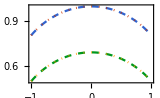

```mathematica
Block[{S1,S2},
S1[n_,d_,m_]:=Block[{q=n(d-2)},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
S2[n_,d_,m_]:=Block[{q=n(d-3)+1},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
S1[d_,m_]:=Log[(Sqrt[π]Gamma[(d-1)/2])/Gamma[d/2]]+(d-2)/2(PolyGamma[d/2]-PolyGamma[(d-1)/2])+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,d/2,m^2];
S2[d_,m_]:=Log[(Sqrt[π]Gamma[(d-1)/2])/Gamma[d/2]]+(d-3)/2(PolyGamma[d/2]-PolyGamma[(d-1)/2])+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,d/2,m^2];
Plot[{S1[1.001,3,m],S1[3,m],S2[1.001,3,m],S2[3,m]},{m,-1,1},PlotStyle->{Dashed,Dotted,Dashed,Dotted},FrameLabel->{"\!\(m\)","\!\(S(m)\)"},ImageSize->160]
]
```

The two different choices of q only leads to a constant shift of the entropy. To determine the background entropy, we take the d→1 limit, where we know that the entropy should converge to that of the Bernoulli distribution

S=-(1+m)/2ln(1+m)/2-(1-m)/2 ln(1-m)/2
=ln 2+1/2_2 F_1^(0,1,0,0)(-1/2,0;1/2;m^2),

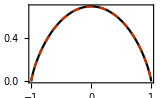

```mathematica
Plot[{Log[2]
+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,1/2,m^2],
-(1+m)/2Log[(1+m)/2]-(1-m)/2Log[(1-m)/2]},{m,-1,1},PlotStyle->{Black,Dashed},FrameLabel->{"\!\(m\)","\!\(S(m)\)"},ImageSize->160]
```

So we identify that S_bg=ln 2 for d=1. To generalize to higher dimension, we notice that 2 is the volume of S^0, i.e. 2=Ω_0. So the systematic generalization should be replacing 2 by Ω_(d-1), such that S_bg=ln Ω_(d-1). This is a reasonable assignment, because when m=0 (polarization vanishes), the dipolar distribution reduces to the uniform distribution on S^(d-1), which should have the entropy S=ln Ω_(d-1). Therefore we conclude that the entropy of the d-dimensional dipolar distribution is given by

S=ln Ω_(d-1)+1/2_2 F_1^(0,1,0,0)(-1/2,0;d/2;m^2)
=ln (2 π^(d/2))/(Γ(d/2))+1/2_2 F_1^(0,1,0,0)(-1/2,0;d/2;m^2).

When m=0, the hypergeometric function vanishes, the entropy ln Ω_(d-1) matches what is expected from the uniform distribution on S^(d-1).

d=1 case. As has appeared in Eq. (DisplayFormulaNumbered), the entropy reduces to that of the Bernoulli distribution

S(m)=-(1+m)/2ln(1+m)/2-(1-m)/2 ln(1-m)/2.

d=3 case. The hypergeometric function can be approached by the Taylor series around m=0,

S(m)=ln(4π)+1/2_2 F_1^(0,1,0,0)(-1/2,0;3/2;m^2)
=ln(4π)-m^2/6-m^4/60-m^6/210-m^8/504-𝒪(m^10).

```mathematica
Series[1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,3/2,m^2],{m,0,8}]//N//Rationalize
```

-m^2/6-m^4/60-m^6/210-m^8/504+O[m]^9

Series expansion.

Some more inspection reveals that the terms in follows the rule of

S(m)=ln(4π)-∑_(k=0)^∞ m^(2k+2)/((2k+1)(2k+2)(2k+3)),

which simplifies to

S(m)=ln(4π)+1/2-(1+m)^2/(4m)ln(1+m)+(1-m)^2/(4m)ln(1-m).

```mathematica
Series[Log[4π]+1/2-(1+m)^2/(4m)Log[1+m]+(1-m)^2/(4m)Log[1-m],{m,0,8}]
```

Log[4 π]-m^2/6-m^4/60-m^6/210-m^8/504+O[m]^9

Verification.

We can numerically check that Eq. (DisplayFormulaNumbered) is indeed equivalent to Eq. (DisplayFormulaNumbered).

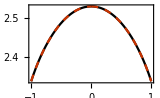

```mathematica
Plot[{Log[4π]+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,3/2,m^2],Log[4π]+1/2-(1+m)^2/(4m)Log[1+m]+(1-m)^2/(4m)Log[1-m]},{m,-1,1},PlotStyle->{Black,Dashed},FrameLabel->{"\!\(m\)","\!\(S(m)\)"},ImageSize->160]
```

#### Outcome Distribution

##### Sampling Unit Vector

Let m(α)=tanh α tanh ϵ, we basically need to sample n from

p(n|α)=1/(4π)(1+n^z m).

```mathematica
Block[{θ=π/6,dθ=π/24},Graphics[{Circle[],AbsoluteThickness[1.2],Line[ReIm/@{0,Exp[ⅈ(π/2-#)]}]&/@{0,θ,θ+dθ},
Line[{ReIm@#,{0,Im@#}}]&/@Exp[ⅈ (π/2-{θ,θ+dθ})],
Circle[{0,0},0.2,(π/2-{0,θ})],Text["θ",{0.1,0.3}],Circle[{0,0},0.4,(π/2-{θ,θ+dθ})],Text["ⅆθ",{0.4,0.3}],Text["\!\(ⅆn\^z\)",{0,Cos[θ]},{1,0.5}]},ImageSize->120]]
```

-Graphics-

We first calculate the marginal distribution of n^z

p(n^z|α)ⅆ n^z=p(n|α)(2π sin θⅆθ),

where 2π sin θ ⅆθ is the area of a belt of width ⅆθ surrounding the sphere on the latitude θ. On the other hand, ⅆ n^z=sin θ ⅆθ, so

p(n^z|α)=2π p(n|α)=1/2(1+n^z m).

The distribution is properly normalized as

∫_-1^1 ⅆ n^zp(n^z|α)=∫_-1^1 ⅆ n^z 1/2(1+n^z m)=1.

So we should first sample n^z from p(n^z|α) given in Eq. (DisplayFormulaNumbered), and then prepend the (n^x,n^y) components. To sample n^z, we first calculate the cumulative distribution function,

f(n^z|α)=∫_-1^(n^z) ⅆ n^zp(n^z|α)=1/4(n^z+1)((n^z-1)m+2).

```mathematica
Integrate[(1+m z)/2,{z,-1,n}]//FullSimplify
```

1/4 (2+m (-1+n)) (1+n)

Integration.

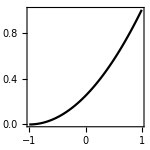

```mathematica
Block[{m=1},
Plot[(n+1)((n-1)m+2)/4,{n,-1,1},FrameLabel->{"\!\(n\^z\)","\!\(f(n\^z|α)\)"},PlotStyle->Black,AspectRatio->1,ImageSize->150]]
```

Then we can take a flow based approach by sampling z∈[0,1] uniformly, and then push it back to n^z by solving the equation of f(n^z|α)=z. The solution is

n^z=(m-2+4z)/(1+√((m-1)^2+4m z)), z\[Distributed]uniform([0,1]).

```mathematica
Solve[(2+m(n-1))(n+1)/4==z,n]
```

{{n→(-1-√(1-2 m+m^2+4 m z))/m},{n→(-1+√(1-2 m+m^2+4 m z))/m}}

Solution.

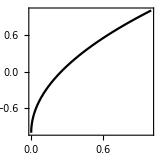

```mathematica
Block[{m=1},
Plot[(m-2+4 z)/(1+Sqrt[(m-1)^2+4m z]),{z,0,1},FrameLabel->{"\!\(z\)","\!\(n\^z\)"},PlotStyle->Black,AspectRatio->1,ImageSize->160]]
```

##### Simulate Weak Measurements

We can use WeakMeasurements[ϵ,N,α0:0] to simulate weak measurements of strength ϵ on N qubits initiated at state of parameter α_0. The result is an association, containing data of α at each step and n as outcomes at each step.

```mathematica
WeakMeasurements[0.1,10,0]
```

<|αs→{0,0.0571878,0.00450611,0.0122992,-0.0222925,0.072805,0.0431786,0.107719,0.123431,0.038227,0.053975},outs→{{0.807263,0.144621,0.572199},{-0.802947,-0.278219,-0.527134},{-0.769664,0.633667,0.0779951},{-0.451155,-0.822572,-0.346171},{0.0387029,-0.3066,0.951051},{-0.087418,-0.951027,-0.29649},{0.696337,-0.313306,0.64572},{0.0743123,0.98476,0.157243},{-0.333791,-0.402845,-0.852232},{-0.532239,0.831794,0.157608}}|>

Distribution of the weak measurement outcomes on a sphere:

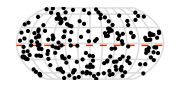
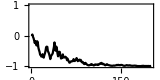

```mathematica
Block[{wm},
wm=WeakMeasurements[0.2,200,0];
Row@{Graphics[{
{LightGray,AbsoluteThickness[1],Line@Table[EEP[{λ,ϕ}],{λ,-π,π,π/6},{ϕ,-π/2,π/2,π/24}],
Line@Table[EEP[{λ,ϕ}],{ϕ,-π/2,π/2,π/6},{λ,{-π,π}}]},
{Dashed,Red,Line[Table[EEP[{λ,#}],{λ,{-π,π}}]]&@ArcSin[Mean[Last/@wm["outs"]]]},
{AbsolutePointSize[3],
Point[EEP[{ArcTan[#1,#2],ArcSin[#3]}]&@@@wm["outs"]]}},ImageSize->180],
ListLinePlot[Tanh[wm["αs"]],PlotStyle->Black,PlotRange->{-1,1},PlotRangePadding->0.1,FrameLabel->{"step","tanh α"},AspectRatio->0.5,ImageSize->160]}]
```

The statistical property is very vague. It is challenging for human to decide which state it collapsed to.

For fixed axis case, it is faster to decohere but the statistical property is still not obvious.

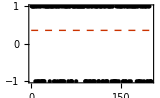
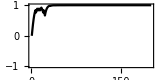

```mathematica
Block[{wm},
wm=WeakMeasurements[0.2,200,0,Axis->"Fixed"];
Row@{ListPlot[wm["outs"],Epilog->{Red,Dashed,Line[Table[{x,#},{x,{0,Length@wm["outs"]}}]]&@Mean[wm["outs"]]},PlotStyle->Directive[Black,AbsolutePointSize[3]],FrameLabel->{"step","\!\(n\^z\)"},ImageSize->160],
ListLinePlot[Tanh[wm["αs"]],PlotStyle->Black,PlotRange->{-1,1},PlotRangePadding->0.1,FrameLabel->{"step","tanh α"},AspectRatio->0.5,ImageSize->160]}]
```

A batch of fixed axis samples. The key feature is the non-local correlation within the same sample.

```mathematica
Grid@Table[Block[{α=0,n=100},
{Style[StringTemplate["\!\(ϵ=`1`\): "][ϵ],14,FontFamily->"CMU"],MatrixPlot[Table[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"],50],ColorFunction->GrayLevel,PlotRangePadding->None,Frame->False,ImageSize->100]}],{ϵ,{0.1,0.2,0.5,1,2}}]
```

ϵ=0.1:  | -Graphics-
ϵ=0.2:  | -Graphics-
ϵ=0.5:  | -Graphics-
ϵ=1:  | -Graphics-
ϵ=2:  | -Graphics-

Note: although the measurement outcomes are collected in a sequential order in the simulation, but they are actually permutation symmetric. Any reshuffling of the data still appears with the same probability.

### Classical World

#### Statistics Analysis

Let us take the case of fixed axis weak measurements. According to Eq. (DisplayFormulaNumbered), the joint distribution is given by

p[n]=(cosh(α+ϵ ∑_(i=1)^N n_i^z))/((2 cosh ϵ)^N cosh α).

Let m=N^-1∑_(i=1)^N n_i^z the magnetization. The distribution of m follows

p(m)=(N
(1+m)/2 N)(cosh(α+ϵ N m))/((2 cosh ϵ)^N cosh α).

As the number N of qubits increases, the distribution of m undergoes a quantum-classical transition at N ϵ^2=1.

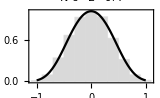

```mathematica
Block[{α=0,ϵ=0.2,n=10},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

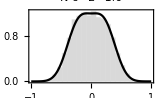

```mathematica
Block[{α=0,ϵ=0.2,n=25},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

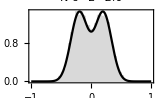

```mathematica
Block[{α=0,ϵ=0.2,n=50},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

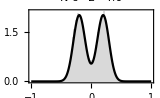

```mathematica
Block[{α=0,ϵ=0.2,n=100},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

Define the variance of the distribution p(m) as

⟨m^2⟩=∫m^2 p(m)ⅆm.

It is found that N⟨m^2⟩ grows linearly with N ϵ^2 starting from 1 as

N⟨m^2⟩=1+N ϵ^2.

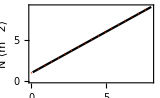

```mathematica
ListLinePlot[{Table[Block[{α=0,ϵ=0.1,n},n=Max[x/ϵ^2,5];{n ϵ^2,n NIntegrate[m^2 n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1}]}],{x,0.1,8,0.1}],Table[{x,1+x},{x,0,8}]},PlotRange->{0,All},PlotStyle->{Black,Dotted},FrameLabel->{"\!\(N ϵ\^2\)","\!\(N ⟨m\^2⟩\)"},ImageSize->160]
```

This implies that the variance can be describe by

⟨m^2⟩=ϵ^2+1/N.

In the large N limit, it saturates to the constant ϵ^2.

#### Transition

Let us first consider the case of α=0. p(m) can be approximated by the action model

p(m)∝e^(-N E(m)),
E(m)=-1/Nln cosh(N ϵ m)-H(m),
H(m)=-(1+m)/2ln(1+m)/2-(1-m)/2 ln(1-m)/2.

Expand around m→0,

E(m)=1/2(1-N ϵ^2)m^2+1/12(1+N^3 ϵ^4)m^4

```mathematica
Series[-Log[Cosh[ϵ m Ν]]/Ν+Log[2]-(-(1+m)/2Log[(1+m)/2]-(1-m)/2Log[(1-m)/2]),{m,0,4}]
```

(1/2-(ϵ^2 Ν)/2) m^2+1/12 (1+ϵ^4 Ν^3) m^4+O[m]^5

Expansion.

This is similar to a Landau potential. A symmetry breaking transition happens at N ϵ^2=1. The saddle point solution is given by

m=Piecewise[{{0, N<ϵ^-2}, {±√((3(N ϵ^2-1))/(N^3 ϵ^4+1)), N>ϵ^-2}}].

```mathematica
Solve[D[(1-Ν ϵ^2)m^2/2+(1+Ν^3 ϵ^4)m^4/12,m]==0,m]
```

{{m→0},{m→-(√3 √(-1+ϵ^2 Ν))/(√(1+ϵ^4 Ν^3))},{m→(√3 √(-1+ϵ^2 Ν))/(√(1+ϵ^4 Ν^3))}}

Solution.

However, this result only holds around the transition, because the expansion Eq. (DisplayFormulaNumbered) is only valid when m is small. Away from the transition, we should find the saddle point directly from Eq. (DisplayFormulaNumbered),

∂_m E(m)=-ϵ tanh(N ϵ m)+arctanh(m),

```mathematica
Block[{H,Ε},
H[m_]:=-Sum[(1+s m)/2Log[(1+s m)/2],{s,{-1,1}}];
Ε[m_]:=-Log[Cosh[ϵ m Ν]]/Ν+Log[2]-H[m];
D[Ε[m],m]//FullSimplify
]
```

ArcTanh[m]-ϵ Tanh[m ϵ Ν]

Derivative.

the saddle point equation ∂_m E(m)=0 suggests

m=tanh(ϵ tanh(N ϵ m)),

which provides us an iterative approach to solve for m.

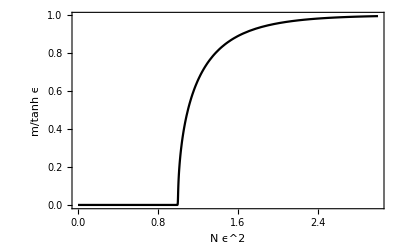

```mathematica
Block[{ϵ=0.1,m},
m[Ν_]:=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
Plot[m[x/ϵ^2]/Tanh[ϵ],{x,0,3},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(m/tanh ϵ\)"}]]
```

In the large N limit (N≫ϵ^-2), m converges to tanh ϵ.

We can follow the saddle point solution and expand E(m) around the saddle point to the quadratic order to obtain a Gaussian model. To calculate the quadratic coefficient, we first evaluate the 2nd order derivative of E(m),

1/(χ(m))≡∂_m^2 E(m)=1/(1-m^2)-N ϵ^2(sech(N ϵ m))^2.

```mathematica
Block[{H,Ε},
H[m_]:=-Sum[(1+s m)/2Log[(1+s m)/2],{s,{-1,1}}];
Ε[m_]:=-Log[Cosh[ϵ m Ν]]/Ν+Log[2]-H[m];
D[Ε[m],{m,2}]//FullSimplify
]
```

1/(1-m^2)-ϵ^2 Ν Sech[m ϵ Ν]^2

Derivative.

Given the saddle point solution m̄(N), the energy expands around it as

E(m)=(m-m̄(N))^2/(2 χ(m̄(N))),

which gives a Gaussian distribution of m

p(m)∝e^(-N E(m))=exp(-(N (m-m̄(N))^2)/(2 χ(m̄(N)))),

so the variance of m goes as

var m=⟨m^2⟩-⟨m⟩^2=1/N χ(m̄(N)).

χ(m̄(N)) is the universal (dimensionless) piece of the variance which does not scale with N. It diverges at the transition point as

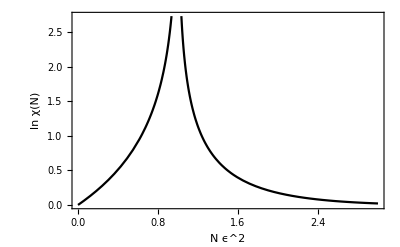

```mathematica
Block[{ϵ=0.1,m,χ},
m[Ν_]:=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
χ[Ν_]:=1/(1/(1-#^2)-ϵ^2 Ν Sech[# ϵ Ν]^2&@m[Ν]);
Plot[Log[χ[x/ϵ^2]],{x,0,3},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(ln χ(N)\)"}]]
```

Conclusion: Because of the phase transition in N, we should not expect the neural network to be able to generalize from small N to large N. We should train the neural network separately at different N.

#### Mode Analysis

In the N>ϵ^-2 phase, the distribution p(m) can be modeled by two Gaussian modes

p(m)=∑_(σ=±) p(m|σ)p(σ)
p(m|σ)=1/(√(2π χ/N))exp(-(N (m-σ m̄)^2)/(2 χ)).

Here we consider that p(±)=1/2, both modes are equal likely to appear. How to quantify the confidence of classification?

##### Misclassification Probability

Let us sample m from p(m|+), what is the probability for m to be classified as -?

p(-|m)=(p(m|-)p(-))/(p(m))=(p(m|-)p(-))/(p(m|+)p(+)+p(m|-)p(-)).

Given p(+)=p(-)=1/2, we have

p(-|m)=(p(m|-))/(p(m|+)+p(m|-)).

Now as we sample from p(m|+), the probability of misclassification is

p_mis=∫ⅆm p(-|m)p(m|+)=∫ⅆm(p(m|-)p(m|+))/(p(m|+)+p(m|-)).

Using the Gaussian model in Eq. (DisplayFormulaNumbered),

p_mis=1/(√(2π χ/N))∫ⅆm/(exp((N (m-m̄)^2)/(2 χ))+exp((N (m+ m̄)^2)/(2 χ)))
=1/(√(2π))∫ⅆx/(e^(1/2 (m-a)^2)+e^(1/2 (m+a)^2)).

where a=m̄/σ_m and σ_m=(χ/N)^(1/2) is the standard deviation.

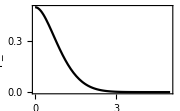

```mathematica
Block[{pmis},
pmis[a_]:=NIntegrate[1/(Exp[(x-a)^2/2]+Exp[(x+a)^2/2]),{x,-∞,∞}]/Sqrt[2π];
Plot[pmis[a],{a,0,5},FrameLabel->{"\!\(m\&_/σ\_m\)","\!\(p\_mis\)"},PlotStyle->Black,ImageSize->180]]
```

Put into the context of transition driven by N, the misclassification drops in the symmetry broken phase.

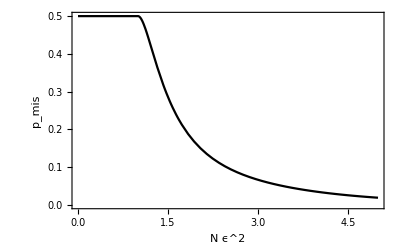

```mathematica
Block[{ϵ=0.1,pmis},
pmis[Ν_]:=Block[{m,χ,a},
m=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
χ=1/(1/(1-m^2)-ϵ^2 Ν Sech[m ϵ Ν]^2);
a=m/Sqrt[χ/Ν];
NIntegrate[1/(Exp[(x-a)^2/2]+Exp[(x+a)^2/2]),{x,-∞,∞}]/Sqrt[2π]];
Plot[pmis[x/ϵ^2],{x,0,5},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(p\_mis\)"}]]
```

##### KL Divergence

A probably more natural way is to average the negative log likely hood of p(-|m) when sampling on p(m|+), this quantifies the amount of surprise that one has to pay to misclassify

NLL=-∫ⅆm p(m|+) ln p(-|m)
=-∫ⅆm p(m|+) ln (p(m|-))/(p(m|+)+p(m|-)).

In the case that p(m|+) and p(m|-) is separated, it is likely that p(m|+)≫p(m|-) for those m sampled from p(m|+), so we can replace p(m|+)+p(m|-) by p(m|+), then Eq. (DisplayFormulaNumbered) becomes the KL divergence

NLL≃∫ⅆm p(m|+) ln (p(m|+))/(p(m|-))=KL(p(m|+)|p(m|-)).

For two Gaussians of equal variance (which is the case for p(m|±)), the KL divergence is simply given by

KL(p(m|+)|p(m|-))=(N ((m̄)_+-(m̄)_-)^2)/(2 χ)=(2N(m̄)^2)/χ.

We can define the confidence by

conf=1-e^(-KL(p(m|+)|p(m|-))).

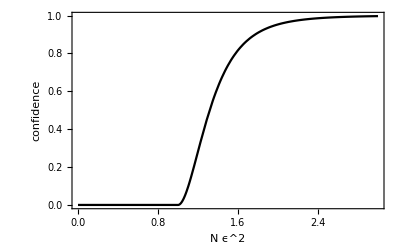

```mathematica
Block[{ϵ=0.1,conf},
conf[Ν_]:=Block[{m,χ},
m=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
χ=1/(1/(1-m^2)-ϵ^2 Ν Sech[m ϵ Ν]^2);
1-Exp[-2Ν m^2/χ]];
Plot[conf[x/ϵ^2],{x,0,3},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(confidence\)"}]]
```

### Latent Space

#### Network Design

Encoder q(z|x): Gaussian, parameterized by mean μ_z and standard deviation σ_z.

q(z|x)∝e^(-(z-μ_z[x])^2/(2σ_z^2[x])).

Decoder p(x|z): dipolar distribution.

p(x|z)∝∏_i (1+x_i m(z)).

Loss (to be minimized)

ℒ=ℒ_re+λ ℒ_kl,
ℒ_re=-𝔼_(z\[Distributed]q(z|x))log p(x|z),
ℒ_kl=KL[q(z|x)|p(z)]=1/2(μ_z^2+σ_z^2-1)-log σ_z,

where the prior p(z) is standard normal.

See Jupyter notebook for details.

#### Saddle Point

Consider a toy model (corresponding to a=c=0) of the VAE, by specifying the following mapping

m(z)=b z, μ_z[x]=d x̄, σ_z[x]=e,

Based on Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we can model the encoder q(z|x) and decoder p(x|z), from which we can further compute the loss function

Reconstruction loss

ℒ_re=-𝔼_(z\[Distributed]q(z|x))log p(x|z)
=-N x̄ b μ_z+1/2 N b^2(μ_z^2+σ_z^2)
=-N b d(x̄)^2+1/2 N b^2(d^2(x̄)^2+e^2)

KL loss

ℒ_kl=KL[q(z|x)|p(z)]
=1/2(μ_z^2+σ_z^2-1)-log σ_z
=1/2 λ(d^2(x̄)^2+e^2-1)-λ log e.

Assemble the total loss with a KL regularization strength λ

ℒ=ℒ_re+λ ℒ_kl
=-N b d(x̄)^2+1/2(N b^2+λ)(d^2(x̄)^2+e^2)-λ log e.

Ensemble average over p(x̄), according to Eq. (DisplayFormulaNumbered),

⟨(x̄)^2⟩=∫ⅆ x̄ (x̄)^2 p(x̄)=ϵ^2+1/N.

Substitute Eq. (DisplayFormulaNumbered) to Eq. Eq. (DisplayFormulaNumbered),

ℒ=-(N ϵ^2+1)b d+1/(2N)(N b^2+λ)(d^2(N ϵ^2+1)+N e^2)-λ log e.

The learning dynamics described by

∂_t b=-N e^2 b-(N ϵ^2+1)d(d b-1),
∂_t d=-1/N(N ϵ^2+1)(λ d+N b (d b-1)),
∂_t e=λ/e-e(N b^2+λ).

```mathematica
FullSimplify[-D[-(Ν ϵ^2+1)b d+1/(2Ν)(Ν b^2+λ)(d^2(Ν ϵ^2+1)+Ν e^2)-λ Log[e],#]]&/@{b,d,e}
```

{d-b e^2 Ν+d ϵ^2 Ν-d^2 (b+b ϵ^2 Ν),-((d λ+b (-1+b d) Ν) (1+ϵ^2 Ν))/Ν,λ/e-e (λ+b^2 Ν)}

Gradient.

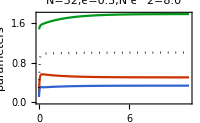

```mathematica
Block[{Ν=32,ϵ=0.5,λ=1,t1=10,b,d,e},
{b,d,e}=NDSolveValue[{
b'[t]==-Ν b[t]e[t]^2-(Ν ϵ^2+1)d[t](b[t]d[t]-1),
d'[t]==-1/Ν(Ν ϵ^2+1)(λ d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t](Ν b[t]^2+λ),
b[0]==ϵ RandomReal[],d[0]==RandomReal[]/ϵ,e[0]==RandomReal[]/Sqrt[Ν]},{b,d,e},{t,0,t1}];
Plot[{b[t],d[t],e[t],b[t]d[t]+e[t]^2},{t,0,t1},PlotStyle->{Red,Green,Blue,Directive[Black,Dotted]},FrameLabel->{"\!\(t\)","parameters"},PlotLabel->StringTemplate["\!\(N=`1`,ϵ=`2`,N ϵ\^2=`3`\)"][Ν,ϵ,Ν ϵ^2],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\)","\!\(b d+e\^2\)"}),ImageSize->200]]
```

Apart from trivial solution b=d=0,e=1, the non-trivial solution is

b=1/(√N)√(1-λ+N ϵ^2),
d=√N(√(1-λ+N ϵ^2))/(1+N ϵ^2),
e=(√λ)/(√(1+N ϵ^2)).

```mathematica
Solve[{d-b e^2 Ν+d ϵ^2 Ν-d^2 (b+b ϵ^2 Ν)==0,(d λ+b (-1+b d) Ν)==0,λ/e-e (λ+b^2 Ν)==0},{b,d,e}]//FullSimplify
```

{{b→0,d→0,e→-1},{b→0,d→0,e→1},{b→-(√(1-λ+ϵ^2 Ν))/(√Ν),d→-(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→-(√λ)/(√(1+ϵ^2 Ν))},{b→-(√(1-λ+ϵ^2 Ν))/(√Ν),d→-(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→(√λ)/(√(1+ϵ^2 Ν))},{b→(√(1-λ+ϵ^2 Ν))/(√Ν),d→(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→-(√λ)/(√(1+ϵ^2 Ν))},{b→(√(1-λ+ϵ^2 Ν))/(√Ν),d→(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→(√λ)/(√(1+ϵ^2 Ν))}}

Solve.

This implies

m(z)=z/(√N)√(1-λ+N ϵ^2),
μ_z[x]=x̄ √N(√(1-λ+N ϵ^2))/(1+N ϵ^2),
σ_z[x]=(√λ)/(√(1+N ϵ^2)).

So the fidelity and the variance are

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z=(1-λ+N ϵ^2)/(1+N ϵ^2),
σ_z^2[x]=λ/(1+N ϵ^2).

Amazingly the fidelity-variance relation still holds

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z+σ_z^2[x]=1.

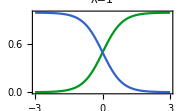

```mathematica
Block[{λ=1},
Plot[Evaluate@Block[{x=10^lgx},{(1-λ+x)/(1+x),λ/(1+x)}],
{lgx,-3,3},PlotStyle->{Green,Blue,Directive[Black,Dotted]},FrameLabel->{"\!\(lg(N ϵ\^2)\)","values"},PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\_z[x]/z\)","\!\(σ\_z\%2[x]\)"}),
PlotLabel->StringTemplate["\!\(λ=`1`\)"][λ],ImageSize->180]]
```

The regularization has the most effect when N ϵ^2 is small, and does not affect the thermodynamic limit. On the other hand, we can also see why λ=1 is the most reasonable choice. Because in the limit of N ϵ^2→0, there is no data to get any clue, and the latent space should remain Gaussian, but this behavior is achieved only when λ=1. Any λ<1 will result in finite fidelity in N ϵ^2→0, which is overfitting.

At λ=1, we find the saddle point solution

b=ϵ, d=(N ϵ)/(1+N ϵ^2), e=1/(√(1+N ϵ^2)),

which amounts to the following maps in the VAE

m(z)=ϵ z, μ_z[x]=(N ϵ)/(1+N ϵ^2)x̄, σ_z^2[x]=1/(1+N ϵ^2).

#### Bifurcation

Suppose p(x̄) has the two-peak structure

p(x̄)=∑_(a=±) p_a exp(-(x̄-μ_a)^2/(2 σ_a)).

The latent space distribution is given by the convolution with the encoding distribution

p(z)=∫ⅆx q(z|x)p(x)
=∑_(a=±) p_a∫ⅆ x̄ exp(-(z-d x̄)^2/(2 e^2))exp(-(x̄-μ_a)^2/(2 σ_a))
=∑_(a=±) p_a exp(-(z-d μ_a)^2/(2(e^2+d^2 σ_a^2))).

```mathematica
Block[{S},
S=-(z-d x)^2/(2e^2)-(x-μ)^2/(2 σ^2);
Simplify[S/.Solve[D[S,x]==0,x]]]
```

{-(z-d μ)^2/(2 (e^2+d^2 σ^2))}

Saddle point.

Even if p(x) bifurcates, p(z) may not, as the Gaussian q(z|x) can further smooth out the distribution and thereby merging bifurcated peaks. Given that

σ_±=1/N,μ_±=±ϵ f(N ϵ^2), d=(N ϵ)/(1+N ϵ^2),e^2=1/(1+N ϵ^2),

where f is the solution of f=tanh(N ϵ^2 f), we can evaluate the effective mean and variance for the latent variable

(μ̃)_a=d μ_a=(N ϵ^2)/(1+N ϵ^2)f(N ϵ^2),
(σ̃)_a^2=e^2+d^2 σ_a^2=(1+2N ϵ^2)/((1+N ϵ^2)^2).

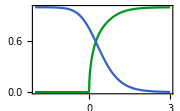

```mathematica
Block[{ϵ=0.1,f},
f[x_]:=FixedPoint[Tanh[x #]&,1,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
ListLinePlot[Thread@Table[Block[{x=10^lgx},{lgx,#}&/@{x/(1+x)f[x],(1+2x)/(1+x)^2}],{lgx,-2,3,0.01}],PlotStyle->{Green,Blue},FrameLabel->{"\!\(lg(N ϵ\^2)\)","values"},PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\&~\_a\)","\!\(\(σ\&~\)\_a\%2\)"}),
ImageSize->180]]
```

## Code

#### Random Vector

```mathematica
RandomVector[m_]:=
Block[{z=RandomReal[],nx,ny,nz},
nz=(m-2+4 z)/(1+Sqrt[(m-1)^2+4m z]);
{nx,ny}=Sqrt[1-nz^2]ReIm@Exp[ⅈ RandomReal[{0,2π}]];
{nx,ny,nz}];
RandomVector[m_,samples_]:=Table[RandomVector[m],samples];
```

#### Weak Measurement

```mathematica
Options[WeakMeasurements]={Axis->"Random"};
WeakMeasurements[ϵ_,Ν_,α0_,OptionsPattern[WeakMeasurements]]:=
Block[{measure,αs,outs},
Switch[OptionValue[Axis],
"Random",
measure[α_]:=Block[{n,nz},
Sow[n=RandomVector[Tanh[α]Tanh[ϵ]]];
nz=Last@n;
α+Log[(1+nz Tanh[ϵ/2])/(1-nz Tanh[ϵ/2])]],
"Fixed",
measure[α_]:=Block[{n},
Sow[n=RandomChoice[{1+Tanh[α]Tanh[ϵ],1-Tanh[α]Tanh[ϵ]}->{1,-1}]];
α+ϵ n]];
{αs,{outs}}=Reap[NestList[measure,α0,Ν]];
<|"αs"->αs,"outs"->outs|>]
```

#### Equal Earth Projection

```mathematica
EEP[{λ_,ϕ_}]:=Block[{θ=ArcSin[Sqrt[3]/2Sin[ϕ]],A1,A2,A3,A4},
{A1,A2,A3,A4}={1.340264,-0.081106,0.000893,0.003796};
{2Sqrt[3]λ Cos[θ]/(3 (9A4 θ^8+7A3 θ^6+3 A2 θ^2+A1)),A4 θ ^9+A3 θ^7+A2 θ^3+A1 θ}]
```

## Draft

### Single Qubit Case

#### Weak Measurement Ensemble

Consider a single qubit generating weak measurement outcomes following the probability distribution

p_dat(x)=(1+x·n)/2,

n is a 3-component vector parametrizing the density matrix of the qubit

ρ=(σ^0+n·σ)/2,

x is a 3-component vector representing the measurement outcome with the associated measurement operator

E_x=(σ^0+x·σ)/2.

It can be verified that Eq. (DisplayFormulaNumbered) is consistent with the measurement theory  p(x)=Tr E_x ρ.

#### Decoder Model

The decoder probability is given by

p(x|z)=(1+x·m(z))/2,

where we assume the decoder to be modeled by (single-layer perceptron, linear-activate-linear)

m(z)=m tanh (w z+b),

with m being a unit vector and w,b being real parameters to learn. The latent representation z is a single real scalar.

We fix the prior probability to normalized Gaussian

p(z)=1/(√(2π))e^(-z^2/2).

Then the model probability distribution is given by

p_mdl(x)=∫ⅆz p(x|z)p(z)=∫ⅆz (1+x·m tanh(w z+b))/(2 √(2π))e^(-z^2/2).

Using the approximation

∫ⅆz/(√(2π))  tanh(w z+b)e^(-z^2/2)≃tanh(b/(√(1+2 w^2))),

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-0.835178}. NIntegrate obtained -1.73472×10^-18 and 8.62339×10^-17 for the integral and error estimates.

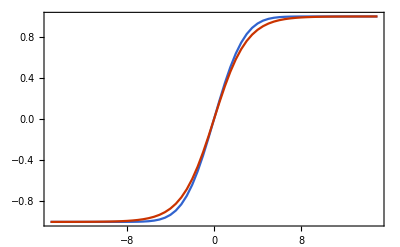

```mathematica
Block[{tanh},
tanh[w_?NumericQ,b_?NumericQ]:=NIntegrate[Tanh[w z+b]Exp[-z^2/2]/Sqrt[2π],{z,-∞,∞}];
Block[{w=2},ListLinePlot@Thread@Table[{{b,tanh[w,b]},{b,Tanh[b/Sqrt[1+2w^2]]}},{b,-15.,15.,0.5}]]]
```

Verification.

we have

p_mdl(x)=(1+x·m tanh(b (1+2 w^2)^(-1/2)))/2.

Comparing with p_dat(x) in Eq. (DisplayFormulaNumbered), the optimal solution should follow from

m tanh(b (1+2 w^2)^(-1/2))=n.

As we over-parametrized the model, the solution is not unique. One idea is to require m to be the unit vector along the direction of n and rescale its length by adjusting b and w.

The tricky part is that for the GHZ state, the reduced density matrix on each single qubit is trivial, i.e. n=0. But hidden behind, there are actually two modes: ±n both happened with 1/2 probability. Each time the system only collapse to one mode, and subsequent weak measurement will confirm the mode. If we train the machine using sequential data produced by one mode, the machine should learn about the preferential axis m to lie along n even if the ensemble does not have a preferential direction n.

Lesson: we can not use sequential measurement (in time) to train, because the sequential data only contain a single mode. ⇒ We should use spacial data to train.

#### Encoder Model

Given the latent prior and the decoder model, the optimal encoder model follows from the Bayes formula

p(z|x)=(p(x|z)p(z))/(p(x))
=1/(√(2π))(1+x·m tanh(w z+b))/(1+x·m tanh(b (1+2 w^2)^(-1/2)))e^(-z^2/2).

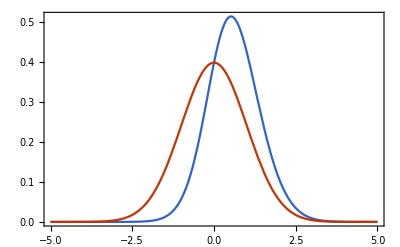

```mathematica
Block[{m={0,0,1},w=1,b=0,pzx},
pzx[z_,x_]:=(1+x.m Tanh[w z+b])/(1+x.m Tanh[b/Sqrt[1+2w^2]])Exp[-z^2/2]/Sqrt[2π];
Block[{x=Normalize@RandomVariate[NormalDistribution[],3]},Plot[{pzx[z,x],Exp[-z^2/2]/Sqrt[2π]},{z,-5,5}]]]
```

It can be approximated by a shifted Gaussian

q(z|x)=1/(√(2π σ))e^(-(z-ζ(x))^2/(2 σ^2)).

If we observe a sequence of x, assuming the events are independent, the inference probability for z follows from the product rule

∏_x q(z|x)∝e^(-∑_x (z-ζ(x))^2/(2 σ^2))=e^(-(N (z-⟨ζ⟩)^2)/(2 σ^2)).

The machine will be confident about its knowledge of z when

σ/(√N)≪⟨ζ⟩.

Moreover, it is possible to keep track of the mean and standard deviation

1/(Σ(T))^2=∑_(t=1:T) 1/(σ(x_t))^2,
Ζ(T)=(Σ(T))^2∑_(t=1:T) (ζ(x_t))/(σ(x_t))^2,

We can then plot Ζ(T)±Σ(T) to see how the mean and standard deviation of the latent variable evolves with respect to time.

Another way to estimate is to use the Bayesian estimation

p(z|{x})=(p({x}|z)p(z))/(p({x}))∝p(z)∏_x p(x|z)

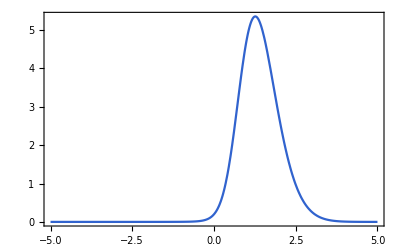

```mathematica
Block[{x=0.1,n=50},
Plot[(1+x Tanh[z])^n/2 Exp[-z^2/2]/Sqrt[2π],{z,-5,5},PlotRange->All]]
```

This also amplifies the bias.

A question to answer is that why measurement must be a many-body effect? If we do not have sufficient number of environment qubits, we will not have sufficient number of observations to establish confidence. So we need to show the confidence curve for different system size and demonstrate that the many-body environment is crucial.

#### Linearized Approximation

Let us consider the simplest case where all neural network functions are linear. Then the decoder model reads

p(x|z)=(1+x·m z)/2,

and the encoder model reads

q(z|x)=1/(√(2π))e^(-(z-x·m')^2/2).

According to Eq. (DisplayFormulaNumbered), the loss function reads

ℒ=𝔼_(z\[Distributed]q(z|x))ln p(x|z)-D_KL(q(z|x)||p(z))
=𝔼_(z\[Distributed]q(z|x))(ln (1+x·m z)/2+(z-x·m')^2/2-z^2/2),

consider that x is a weak measurement outcome which is close to zero, we can approximate

ln(1+x·m z)≃x·m z-(x·m)^2 z^2/2+…

therefore

ℒ=𝔼_(z\[Distributed]q(z|x))(x·(m-m')z-(x·m)^2 z^2/2+1/2(x·m')^2)
=x·(m-m') x·m'-(x·m)^2 (1+(x·m')^2)/2+1/2(x·m')^2
=-1/2 (x·m)^2(x·m')^2-1/2(x·(m-m'))^2.

Further average over x\[Distributed]p_dat(x),

ℒ=-1/2 m^2 m'^2-1/2(m-m')^2,

so maximizing ℒ leads to a trivial result m=m'=0. This implies that either linearized model is not good enough or the single-qubit signal can not drive the VAE to learn about the classical modes.

### IOVM Idea

#### Spherical POVM

##### On-Site Case

Define the single-qubit IOVM (where )

E_m=(σ^0+m·σ)/2.

We have

trace properties

Tr E_m=1, Tr E_m E_m'=(1+m·m')/2,

isometry (assuming ∫_(S^2) ⅆm =1)

∫_(S^2) ⅆm E_m⊗E_m ᵀ
=1/4∫_(S^2) ⅆm (σ^0+m·σ)⊗(σ^0+m·σ)ᵀ
=1/4∫_(S^2) ⅆm (σ^0+m_1 σ^1+m_2 σ^2+m_3 σ^3)⊗(σ^0+m_1 σ^1-m_2 σ^2+m_3 σ^3)
=1/4(σ^00+m^2/3(σ^11-σ^22+σ^33)).

```mathematica
Integrate[x^2,{x,y,z}∈Sphere[]]/(4π)
```

1/3

Details.

Therefore if we choose m^2=3, we can obtain

∫_(S^2) ⅆm E_m⊗E_m ᵀ=1/2(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
Represent[σ[0,0]+σ[1,1]-σ[2,2]+σ[3,3]]//MatrixForm
```

(2 | 0 | 0 | 2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
2 | 0 | 0 | 2)

Details.

In terms of diagrams,

=1/2.

It corresponds to the projection operator of EPR state along the vertical direction, but it also gives the isometry along the horizontal direction.

##### Many-Body Case

For multiple sites, we define

the indefinite-operator valued measure (IOVM)

E[m]=⊗_i(1+m_i·σ_i)/2,

the measurement operator (overs non-local observables)

M[x]=1/2(1+∑_[μ] x_[μ]σ^[μ]).

The Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) generalized to

Tr E[m]=1,
Tr M[x]E[m]=1/2(1+∑_[μ] x_[μ]∏_i m_i^μ_i).

∫ⅅ[m] E[m]⊗E[m]ᵀ=2^-n id.

Given a density matrix ρ, we can generate a joint probability distribution

p[m]=2^n Tr E[m]ᵀρ.

such that the density matrix can be reconstructed by

ρ=∫ⅅ[m]E[m]p[m],

which gives the proposed model in Eq. (DisplayFormulaNumbered). However, since E[m]ᵀ is not positive definite, this makes p[m] potentially indefinite as well, which causes a problem. But in practice, it seems that p[m] might still exist for certain states (e.g. the EPR state).

Under measurement, the probability to generate the outcome x is

p(x)=Tr M[x]ρ=∫ⅅ[m]p(x|m)p[m],
p(x|m)=Tr M[x]E[m].

Again, there is no guarantee that p(x|m) is positive definite.

Comments:

If we restrict m to be unit vectors, then E[m] is a POVM, but we can not establish the isometry from the contraction of E[m]⊗E[m]ᵀ, and the tomography will fail. The fundamental reason is that the POVM model can not capture all the entanglement structure of a density matrix.

If we generalize m to be arbitrary vectors, then E[m] is no longer positive definite, but the isometry can be established, and the state tomography can be realized. But working with indefinite operator E[m], the conditional probability of measurement outcome p(x|m)=Tr M[x]E[m] can be negative. The workaround is to consider weak enough measurement to avoid negative p(x|m).

#### Representing EPR State

EPR state (2-qubit)

EPR=1/(√2)(00+11).

Density matrix

ρ=EPREPR=1/4(σ^00+σ^11-σ^22+σ^33).

```mathematica
Abstract[#⊗#&@(SparseArray[{1->1,-1->1},4]/Sqrt[2])]
```

1/4 σ[0,0]+1/4 σ[1,1]-1/4 σ[2,2]+1/4 σ[3,3]

Details.

Distribution of m, according to Eq. (DisplayFormulaNumbered),

p[m]=4Tr E[m]ᵀρ=1+m11 m21-m12 m22+m13 m23,

```mathematica
4σTr[σTranspose[CircleTimes@@Table[(σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}])/2,{i,2}]]·Abstract[#⊗#&@(SparseArray[{1->1,-1->1},4]/Sqrt[2])]]//Expand
```

1+m11 m21-m12 m22+m13 m23

Details.

where m_(1,2) is assumed to be on a sphere of √3 length. One can see that p[m] indeed become negative, e.g. when m_1=m_2=(0,√3,0), p[m]=-2. This seems to be a problem. But one may question if Eq. (DisplayFormulaNumbered) is the only solution for p[m]. Since the only key is to produce the desired expectation for the polynomials of m, there might be other solution of p[m] that can achieve the same expectations. To check this, we first evaluate the expectation values based on the indefinite distribution in Eq. (DisplayFormulaNumbered). We can indeed verify that

𝔼[m11 m21]=-𝔼[m12 m22]=𝔼[m13 m23]=1,

```mathematica
Integrate[m1⊗m2(1+9m1.DiagonalMatrix[{1,-1,1}].m2),m1∈Sphere[],m2∈Sphere[]]/(4π)^2
```

{{1,0,0},{0,-1,0},{0,0,1}}

Integrate.

and the remaining expectations are zero. However, the same expectations can be reproduced by another positive definite p[m]

p[m]=δ(m_1=n)δ(m_2=(1,-1,1)⊙n),

where n is uniformly distributed on a sphere of √3 length.

Conclusion:

What is important is the expectation value not the distribution. There are multiple possibilities of p[m] that gives the same expectation, we need to pick the positive ones.

The isometry relation is not useful, because p[m] in Eq. (DisplayFormulaNumbered) obtained from isometry relation is not the positive definite one. By using the trace formula Tr E[m]ᵀρ to construct the distribution, the result always looks like 1+… as Eq. (DisplayFormulaNumbered), then we are wasting our positivity on this background shift 1 of the distribution (we are weakening the sharpness of the distribution, and hence we will have to use negative probabilities somewhere to compensate).

#### Representing GHZ State

GHZ state (multiple qubits)

GHZ=1/(√2)(0… 0+1… 1).

Density matrix ρ=GHZGHZ. Now we assume that ρ is given by Eq. (DisplayFormulaNumbered), we have

∫ⅅ[m]E[m]p[m]=GHZGHZ.

By comparing both sides of Eq. (DisplayFormulaNumbered), we can obtain the required expectation of m_i=(m_i1,m_i2,m_i3) under p[m]. In the following, we only present the non-trivial expectation values.

2-qubit

```mathematica
Block[{n=2},DeleteCases[Reduce@First@Last@Reap[Collect[Collect[CircleTimes@@Table[σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}],{i,n}],_σ,𝔼]-Abstract[2^(n-1)#⊗#&@SparseArray[{1->1,-1->1},2^n]],_σ,Sow[#==0]&];],_==0]]
```

𝔼[1]==1&&𝔼[m11 m21]==1&&𝔼[m12 m22]==-1&&𝔼[m13 m23]==1

4-qubit

```mathematica
Block[{n=4},DeleteCases[Reduce@First@Last@Reap[Collect[Collect[CircleTimes@@Table[σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}],{i,n}],_σ,𝔼]-Abstract[2^(n-1)#⊗#&@SparseArray[{1->1,-1->1},2^n]],_σ,Sow[#==0]&];],_==0]]
```

𝔼[1]==1&&𝔼[m33 m43]==1&&𝔼[m23 m43]==1&&𝔼[m23 m33]==1&&𝔼[m11 m21 m31 m41]==1&&𝔼[m11 m21 m32 m42]==-1&&𝔼[m11 m22 m31 m42]==-1&&𝔼[m11 m22 m32 m41]==-1&&𝔼[m12 m21 m31 m42]==-1&&𝔼[m12 m21 m32 m41]==-1&&𝔼[m12 m22 m31 m41]==-1&&𝔼[m12 m22 m32 m42]==1&&𝔼[m13 m43]==1&&𝔼[m13 m33]==1&&𝔼[m13 m23]==1&&𝔼[m13 m23 m33 m43]==1

6-qubit

```mathematica
Block[{n=6},DeleteCases[Reduce@First@Last@Reap[Collect[Collect[CircleTimes@@Table[σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}],{i,n}],_σ,𝔼]-Abstract[2^(n-1)#⊗#&@SparseArray[{1->1,-1->1},2^n]],_σ,Sow[#==0]&];],_==0]]
```

𝔼[1]==1&&𝔼[m53 m63]==1&&𝔼[m43 m63]==1&&𝔼[m43 m53]==1&&𝔼[m33 m63]==1&&𝔼[m33 m53]==1&&𝔼[m33 m43]==1&&𝔼[m33 m43 m53 m63]==1&&𝔼[m23 m63]==1&&𝔼[m23 m53]==1&&𝔼[m23 m43]==1&&𝔼[m23 m43 m53 m63]==1&&𝔼[m23 m33]==1&&𝔼[m23 m33 m53 m63]==1&&𝔼[m23 m33 m43 m63]==1&&𝔼[m23 m33 m43 m53]==1&&𝔼[m11 m21 m31 m41 m51 m61]==1&&𝔼[m11 m21 m31 m41 m52 m62]==-1&&𝔼[m11 m21 m31 m42 m51 m62]==-1&&𝔼[m11 m21 m31 m42 m52 m61]==-1&&𝔼[m11 m21 m32 m41 m51 m62]==-1&&𝔼[m11 m21 m32 m41 m52 m61]==-1&&𝔼[m11 m21 m32 m42 m51 m61]==-1&&𝔼[m11 m21 m32 m42 m52 m62]==1&&𝔼[m11 m22 m31 m41 m51 m62]==-1&&𝔼[m11 m22 m31 m41 m52 m61]==-1&&𝔼[m11 m22 m31 m42 m51 m61]==-1&&𝔼[m11 m22 m31 m42 m52 m62]==1&&𝔼[m11 m22 m32 m41 m51 m61]==-1&&𝔼[m11 m22 m32 m41 m52 m62]==1&&𝔼[m11 m22 m32 m42 m51 m62]==1&&𝔼[m11 m22 m32 m42 m52 m61]==1&&𝔼[m12 m21 m31 m41 m51 m62]==-1&&𝔼[m12 m21 m31 m41 m52 m61]==-1&&𝔼[m12 m21 m31 m42 m51 m61]==-1&&𝔼[m12 m21 m31 m42 m52 m62]==1&&𝔼[m12 m21 m32 m41 m51 m61]==-1&&𝔼[m12 m21 m32 m41 m52 m62]==1&&𝔼[m12 m21 m32 m42 m51 m62]==1&&𝔼[m12 m21 m32 m42 m52 m61]==1&&𝔼[m12 m22 m31 m41 m51 m61]==-1&&𝔼[m12 m22 m31 m41 m52 m62]==1&&𝔼[m12 m22 m31 m42 m51 m62]==1&&𝔼[m12 m22 m31 m42 m52 m61]==1&&𝔼[m12 m22 m32 m41 m51 m62]==1&&𝔼[m12 m22 m32 m41 m52 m61]==1&&𝔼[m12 m22 m32 m42 m51 m61]==1&&𝔼[m12 m22 m32 m42 m52 m62]==-1&&𝔼[m13 m63]==1&&𝔼[m13 m53]==1&&𝔼[m13 m43]==1&&𝔼[m13 m43 m53 m63]==1&&𝔼[m13 m33]==1&&𝔼[m13 m33 m53 m63]==1&&𝔼[m13 m33 m43 m63]==1&&𝔼[m13 m33 m43 m53]==1&&𝔼[m13 m23]==1&&𝔼[m13 m23 m53 m63]==1&&𝔼[m13 m23 m43 m63]==1&&𝔼[m13 m23 m43 m53]==1&&𝔼[m13 m23 m33 m63]==1&&𝔼[m13 m23 m33 m53]==1&&𝔼[m13 m23 m33 m43]==1&&𝔼[m13 m23 m33 m43 m53 m63]==1

We conclude that the expectation values of m for the GHZ state are given by the following general rules

∀A∈Subset[{1,…,n},even]:
𝔼[∏_(i∈A) m_i3]=1,

∀a_i=1,2&{a_i} has even number of 2:
𝔼[∏_(i=1)^n m_(i a_i)]=∏_(i=1)^n ⅈ^(δ(a_i==2)).

We may reproduce these behaviors by assuming m_ia to be Ising variables,

m_ia=(-)^z_ia=±1, z_ia∈ℤ_2.

The requirements in Eq. (DisplayFormulaNumbered) can be easily achieved. We only need to assign

m_13=m_23=…=m_n3=±1,

meaning that all the 3rd component of m_i are the same and take values in ±1 with equal probability.

Eq. (DisplayFormulaNumbered) is harder to deal with. We must make sure that these conditions do not contradict with each other and also do not rule out all degrees of freedoms in the system. For a size-n system, there are 2n in-plane (1 and 2) components of m_i. Assuming them to be Ising variables, we have totally 2n of them. What about the number of constrains? The number of constrains is given by

∑_(k=0)^(n/2) C_n^(2k)=2^(n-1).

```mathematica
Sum[Binomial[n,2k],{k,0,n/2}]
```

2^(-1+n)

Sum.

So the number of constrains grows exponentially with n which is must faster than the linear grow of the number of variables 2n. In fact for n>4, we always have more constrains. The constrains can be expressed in a linear algebra approach using the ℤ_2 variable z_ia=0,1,

∑_(i a) z_(i a)P_(i a,k)=b_k,

where k labels the constrain and P_(i a,k) is a ℤ_2 matrix and b_k=0,1 denotes the constrain.

We can first check that the ℤ_2 rank of P, which is the number of independent constrains. We found

rank_ℤ_2 P=n,

```mathematica
Table[Block[{P},
P=SparseArray[Flatten[MapIndexed[Table[{ia,First@#2}->1,{ia,#1}]&,Join[Complement[Range[n],#],n+#]&/@Subsets[Range[n],{0,n,2}]]],{2n,2^(n-1)}];
n->MatrixRank[P,Modulus->2]],{n,2,6}]
```

{2→2,3→3,4→4,5→5,6→6}

MatrixRank.

meaning that P is not full ranked. Note that there are 2n variables, but only n independent constraint, so there remain n independent free variables.

Unfortunately, the solution of Eq. (DisplayFormulaNumbered) only exists for n=2. For larger n, the constrains contradict with each other and there is no solution.

```mathematica
Block[{n=3,P,b},
P=SparseArray[Flatten[MapIndexed[Table[{ia,First@#2}->1,{ia,#1}]&,Join[Complement[Range[n],#],n+#]&/@Subsets[Range[n],{0,n,2}]]],{2n,2^(n-1)}];
b=Mod[(Length/@Subsets[Range[n],{0,n,2}])/2,2];
LinearSolve[Transpose[P],b,Modulus->2];
Column@{MatrixForm[{b}],MatrixForm[P]}->Column@{MatrixForm[{b}],MatrixForm[RowReduce[P,Modulus->2]]}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

(0 | 1 | 1 | 1)
(1 | 0 | 0 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 1 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1)→(0 | 1 | 1 | 1)
(1 | 0 | 0 | 1
0 | 1 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

However, this is not the end of the story. Because in Eq. (DisplayFormulaNumbered), we have shown that there exist a set of tetra IOVM, which has been proven to be able to do tomography. The above failure only indicates that the assumption that all components of m are Ising variables is problematic, this restricts m_i to the 8 corners of a cube, which is actually not invertible.

### Latent Space

#### Entropy of Dipolar Distribution

```mathematica
Block[{d=3,n=2,p},
p[θ_]:=(1+m Cos[θ])/(2π^(d/2)/Gamma[d/2]);{Integrate[p[θ]^n 2π^((d-1)/2)/Gamma[(d-1)/2]Sin[θ]^(d-2),{θ,0,π}],Simplify[2π^((d-1)/2)Gamma[n+1]/(2π^(d/2)/Gamma[d/2])^n 
Sum[m^k Gamma[(k+1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]}]
```

{(3+m^2)/(12 π),(3+m^2)/(12 π)}

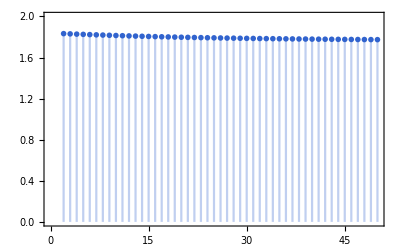

```mathematica
Block[{d=2,m=0.1,S},
S[n_]:=Log[2π^((d-1)/2)Gamma[n+1]/(2π^(d/2)/Gamma[d/2])^n 
Sum[m^k Gamma[(k+1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]/(1-n);
DiscretePlot[S[n],{n,2,50},PlotRange->{0,2}]]
```

```mathematica
Block[{S},
S[n_]:=Log[2π^((d-1)/2)Gamma[n+1]/(2π^(d/2)/Gamma[d/2])^n 
Sum[m^k Gamma[(k+1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]/(1-n);
S[2]//FullSimplify]
```

Log[2]-Log[((d+m^2) π^(-d/2) Gamma[d/2])/d]

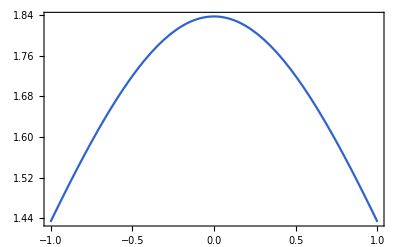

```mathematica
Block[{d=2},
Plot[-Log[(1+m^2/d)/(2π^(d/2)/Gamma[d/2])],{m,-1,1}]]
```

```mathematica
Block[{d=2,n=2},
2π^((d-1)/2)/Gamma[(d-1)/2]/(2π^(d/2)/Gamma[d/2])^n Integrate[(1+m Cos[θ])^n Sin[θ]^(d-2),{θ,0,π}]]
```

(2+m^2)/(4 π)

```mathematica
Block[{d=4},Integrate[(1+m Cos[θ])^n Sin[θ]^(d-2),{θ,0,π}]]
```

1/8 (4+m^2) π

```mathematica
Integrate[Cos[θ]^a Sin[θ]^b,{θ,0,π}]
```

ConditionalExpression[((1+(-1)^a) Gamma[(1+a)/2] Gamma[(1+b)/2])/(2 Gamma[1/2 (2+a+b)]),Re[a]>-1&&Re[b]>-1]

```mathematica
Block[{d=3,n=2},
Simplify[2π^((d-1)/2)/Gamma[(d-1)/2]/(2π^(d/2)/Gamma[d/2])^n 

Sum[m^k (Gamma[n+1]Gamma[(k+1)/2]Gamma[(d-1)/2])/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]]
```

(3+m^2)/(12 π)

```mathematica
Gamma[n+1]Gamma[(k+1)/2]Gamma[(d-1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2])/.{n->1,k->0}
```

(√π Gamma[1/2 (-1+d)])/Gamma[d/2]

#### Loss Function

Let us focus on the fixed axis model and try to understand how the optimization works. In this case, x=(…,x_i,…) is a string of x_i=±1. To simplify the problem, we will further assume that the latent space is one-dimensional z∈ℝ.

We first evaluate the reconstruction loss. According to Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered),

ℒ_re=-𝔼_(z\[Distributed]q(z|x))log p(x|z)
=-1/(√(2π)σ_z)∫∑_i log(1+x_i m(z))exp(-(z-μ_z)^2/(2 σ_z^2))ⅆz.

In the weak measurement limit, x_i m(z) is expected to be small, so we can expand the logarithm

log(1+x_i m(z))≃x_i m(z)-(x_i^2(m(z))^2)/2.

Substitute Eq. (DisplayFormulaNumbered) to Eq. (DisplayFormulaNumbered), we have

ℒ_re≃-∑_i x_i ⟨m(z)⟩+1/2∑_i x_i^2⟨(m(z))^2⟩
=-N x̄⟨m(z)⟩+1/2 N OverBar[x^2]⟨(m(z))^2⟩,

where we have introduce the bracket notation for average under the Gaussian distribution of latent variable

⟨□⟩=1/(√(2π)σ_z)∫□exp(-(z-μ_z)^2/(2 σ_z^2))ⅆz,

and we have defined

x̄=1/N∑_i x_i, OverBar[x^2]=1/N∑_i x_i^2.

For our data set, OverBar[x^2] is basically a constant. For the fixed axis case, x_i=±1, so OverBar[x^2]=1 precisely. For the random axis case, in the weak measurement limit, OverBar[x^2]=1/3 is pretty stable. As we are considering the fixed axis model, we will just set OverBar[x^2] to identity.

As m(z) is a ℝ→ℝ function, it admits the power series expansion

m(z)≃a+b z+….

Here we assume z to be small and truncate the expansion at linear order. With this Eq. (DisplayFormulaNumbered) becomes

ℒ_re=-Nx̄(a+b ⟨z⟩)+1/2 N (a^2+2a b ⟨z⟩+b^2⟨z^2⟩),

and ⟨z^k⟩ is the kth moment of the latent distribution. Based on Eq. (DisplayFormulaNumbered), we have

⟨z^1⟩=μ_z,⟨z^2⟩=μ_z^2+σ_z^2,

so Eq. (DisplayFormulaNumbered) becomes

ℒ_re=-Nx̄(a+b μ_z)+1/2 N (a^2+2a b μ_z+b^2(μ_z^2+σ_z^2)),

Combining with the KL loss

ℒ_kl=1/2(μ_z^2+σ_z^2-1)-log σ_z,

the total loss is

ℒ=-Nx̄(a+b μ_z[x])+1/2 N (a^2+2a b μ_z[x]+b^2(μ_z^2[x]+σ_z^2[x]))+1/2(μ_z^2[x]+σ_z^2[x]-1)-log σ_z[x].

Both μ_z and σ_z will be function of the input x. Together with them, coefficients a and b will also be the variational.

The loss will be evaluated on the data set, where x is drawn form the distribution p(x).

#### Gradient Descent Dynamics

The functional optimization is still difficult to analyze. Based on our numerical observation, the VAE somehow (magically) learns to make μ_z linear in x̄ and σ_z to be a constant. If we follow this ansatz

μ_z[x]=c+d x̄, σ_z[x]=e,

the loss function becomes

ℒ=-Nx̄(a+b (c+d x̄))+1/2 N (a^2+2a b  (c+d x̄)+b^2( (c+d x̄)^2+e^2))+1/2( (c+d x̄)^2+e^2-1)-log e.

See Eq. (DisplayFormulaNumbered) for a simplified version with a=c=0 and KL regularization.

For the parameter θ=a,b,c,d,e, the learning dynamics is generally given by the gradient descent

∂_t θ=-∂_θ ℒ.

We obtain the dynamical equation of parameters

∂_t a=-N(a+b c)-N x̄(b d-1),
∂_t b=-N(a c+b (c^2+e^2))-N x̄((a +2 b c) d-c)-N (x̄)^2 d(b d-1),
∂_t c=-(c+N b (a+b c))- x̄(d+N b(b d-1)),
∂_t d=- x̄(c+N b (a+b c))- (x̄)^2(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

```mathematica
Collect[-D[-Ν x(a+b (c+d x))+Ν/2(a^2+2a b(c+d x)+b^2((c+d x)^2+e^2))+1/2((c+d x)^2+e^2)-Log[e],#],x,Expand]&/@{a,b,c,d,e}
```

{-a Ν-b c Ν+x (Ν-b d Ν),-a c Ν-b c^2 Ν-b e^2 Ν+x (c Ν-a d Ν-2 b c d Ν)+x^2 (d Ν-b d^2 Ν),-c-a b Ν-b^2 c Ν+x (-d+b Ν-b^2 d Ν),x (-c-a b Ν-b^2 c Ν)+x^2 (-d+b Ν-b^2 d Ν),1/e-e-b^2 e Ν}

Derivatives.

Let us first analyze the dynamics of e=σ_z. Without KL regularization, it follows ∂_t e=-N b^2 e, under which e flows to 0 inevitably. KL regularization plays an important role to maintain a finite variance

e^2=1/(1+N b^2).

Note: if the KL loss strength is controlled by λ (i.e. ℒ=ℒ_re+λ ℒ_kl), the saddle point is give by e^2=λ/(N b^2+λ).

```mathematica
e^2/.Solve[λ(1/e-e)-Ν b^2e==0,e]
```

{λ/(λ+b^2 Ν),λ/(λ+b^2 Ν)}

Solve

#### Saddle Point Solutions

In the batch training, the r.h.s. of the differential equation Eq. (DisplayFormulaNumbered) will be evaluated in an ensemble of input samples x (each has a different x̄ following the distribution p(x̄) that may bifurcate). Every power of x̄ should be ensemble averaged. Let us consider the case with reflection symmetry, i.e. p(x̄)=p(-x̄), then x̄ averages to 0. We define the average of (x̄)^2 to be

ϵ^2=∫ⅆ x̄ (x̄)^2 p(x̄).

The ensemble average can also be done on the level of loss function. It is very important to assume that ϵ^2 is independent of N. If x were a collection of independent Gaussian variables, the mean x̄ would follow a Gaussian distribution with a variance that decreases with N, as ϵ^2∼1/N, then the distribution p(x̄) will not bifurcate but just become more concentrated. The fact that p(x̄) bifurcates indicates that ϵ^2 will stop decreasing with N when bifurcation has happened.

Then Eq. (DisplayFormulaNumbered) becomes

∂_t a=-N(a+b c),
∂_t b=-N(a c+b (c^2+e^2))-N ϵ^2 d(b d-1),
∂_t c=-(c+N b (a+b c)),
∂_t d=- ϵ^2(d+N b(b d-1)).

This is still complicated. Let us further take the large-N limit, but keep N ϵ^2 fixed at order one, the leading terms will be

∂_t a=-N(a+b c),
∂_t b=-N c (a+b c),
∂_t c=-N b (a+b c),
∂_t d=-N ϵ^2 b (b d-1).

There are two saddle point solutions:

Type A (trivial, forgetful)

a=b=0,c,d∈ℝ,e=1
⇒m(z)=0, μ_z=c+d x̄,σ_z=1.

Type B (nontrivial, following)

a=-b c,b d=1,e=N^(-1/2) b^-1
⇒m(z)=(z-c)/d→x̄, μ_z=c+d x̄,σ_z=d N^(-1/2).

```mathematica
Solve[{a+b c==0,a c+b(c^2)==0,b(a+b c)==0,b(b d-1)==0},{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0,b→0},{a→-b c,d→1/b}}

Solve.

Now let us put the saddle point solutions back to Eq. (DisplayFormulaNumbered), so as to analyze the sub-leading effects.

Type A saddle (a=b=0,c,d∈ℝ,e=1)

∂_t a=0,
∂_t b=-N b (c^2+e^2)+N ϵ^2 d,
∂_t c=-c,
∂_t d=- ϵ^2d.

We can see that c,d will decay to zero. But the flow of d is very slow (of the rate ϵ^2). While d is finite, it tends to drive the growth of b in the same direction as d, but the dominate decay term in b will control b at a very low level b=ϵ^2 d (c^2+1)^-1 which will also slowly vanish as d vanishes. So in the long time limit, the ultimate type A saddle is

a=b=c=d=0, e=1
⇒m(z)=0, μ_z[x]=0,σ_z[x]=1.

Type B saddle (a=-b c,b d≃1,e=N^(-1/2) b^-1)

∂_t a=0
∂_t b=-b^-1-N ϵ^2 d(b d-1),
∂_t c=-c,
∂_t d=- ϵ^2(d+N b(b d-1)).

The dynamics of a,c is relatively simple: they just exponentially decay to zero, the decay of c is driven by the KL regulation gradually, a will quickly follow c as a=-b c, together they vanish.

The dynamics of b,d is more complicated. We can not assume b d=1 to hold exactly. The saddle point solution is (the sign of b and d are correlated to be the same)

b=±ϵ/2(1+√(1-4/(N ϵ^2))),
d=±1/ϵ.

```mathematica
Solve[{1/b+Ν ϵ^2 d(b d-1)==0,d+Ν b(b d-1)==0},{b,d}]//FullSimplify
```

{{b→-ϵ/2-(√(-4+ϵ^2 Ν))/(2 √Ν),d→-1/ϵ},{b→1/2 (ϵ-(√(-4+ϵ^2 Ν))/(√Ν)),d→1/ϵ},{b→1/2 (-ϵ+(√(-4+ϵ^2 Ν))/(√Ν)),d→-1/ϵ},{b→1/2 (ϵ+(√(-4+ϵ^2 Ν))/(√Ν)),d→1/ϵ}}

Solve.

Interestingly, the solution only exist for N ϵ^2≥4.

In the long time limit, the ultimate type B saddle is

a=c=0, b=(ϵ/2)(1+(1-4/N ϵ^2)^(1/2)),d=1/ϵ,e=1/(√(1+N b^2))
⇒m(z)=ϵ/2(1+√(1-4/(N ϵ^2)))z,
 μ_z[x]=(x̄)/ϵ,
σ_z[x]=√(1/2(1-√(1-4/(N ϵ^2)))).

It turns out that the saddle point solution is only valid in large N ϵ^2. The singularity at N ϵ^2=4 is not observed in actual numerics (by solving Eq. (DisplayFormulaNumbered)). We may have made some mistake in the above analysis.

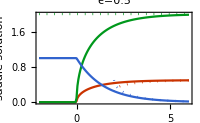

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{b[t1],ϵ/2(1+Sqrt[1-4/(Ν ϵ^2)]),d[t1],1/ϵ,e[t1]^2,1/2(1-Sqrt[1-4/(Ν ϵ^2)])}],{lgΝ,0,8,0.05}],
PlotStyle->{Red,Directive[Dotted,Red],Green,Directive[Dotted,Green],Blue,Directive[Dotted,Blue]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","saddle solution"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\) actual","\!\(b\) large-N","\!\(d\) actual","\!\(d\) large-N","\!\(e\^2\) actual","\!\(e\^2\) large-N"}),ImageSize->200]]
```

##### Implications of Type B Saddle

We expect that the standard deviation σ_z of the encoding distribution q(z|x) consistently drops with N ϵ^2. The dependence is universal.

σ_z^2[x]=1/2(1-√(1-4/(N ϵ^2))).

The following figure shows this dependence, red: analytic formula from Eq. (DisplayFormulaNumbered), black: machine learning result (on random axis model). The trend is consistent. The details don’t quite match because the models are different, or the training has not converged.

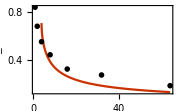

```mathematica
Show[{Plot[{Sqrt[(1-Sqrt[1-4/x])/2]},{x,4,64},PlotStyle->Red,PlotRange->{0,All}],ListPlot[{{1,0.84},{2,0.68},{4,0.55},{8,0.44},{16,0.32},{32,0.27},{64,0.18}}.{{1,0},{0,1}},PlotStyle->Black]},FrameLabel->{"\!\(N ϵ\^2\)","\!\(σ\_z\)"},ImageSize->180]
```

We can also investigate how the polarization m(μ_z) follows the magnetization x̄. We use the ratio to quantify how well the fidelity of the autoencoder in the data space. The ratio increases with N ϵ^2, and the behavior is universal.

(m(μ_z[x]))/(x̄)=1/2(1+√(1-4/(N ϵ^2))).

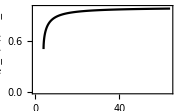

```mathematica
Plot[(1/2)(1+Sqrt[1-4/x]),{x,0,64},PlotRange->{0,1},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(m(μ\_z(x))/x\&_\)"},ImageSize->180]
```

We can also quantify the fidelity of the autoencoder in the latent space. This amounts to ask, given a latent variable z, generate the configuration x (whose mean x̄ is given by m(z)), then infer the latent representation, how much we can recover the latent variable? This gives the same ratio

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z=1/2(1+√(1-4/(N ϵ^2))).

Interestingly, the latent space fidelity and the latent space variance add up to a constant

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z+σ_z^2[x]=1.

This relation could be universal to the task?

##### Effect of KL Regulation

If we consider the KL loss appears with strength λ, the solution of e^2 is modified to

e^2=λ/(N b^2+λ).

Consider the Type B saddle point, where a=-b c, Eq. (DisplayFormulaNumbered) becomes (we will only focus on the equations for b and d)

∂_t b=-λ/b-N ϵ^2 d(b d-1),
∂_t d=- ϵ^2(λ d+N b(b d-1)).

We obtain the saddle point solution

b=ϵ/2(1+√(1-(4λ)/(N ϵ^2))),
d=1/ϵ,
e^2=1/2(1-√(1-(4λ)/(N ϵ^2))).

```mathematica
Solve[{λ/b+Ν ϵ^2d(b d-1)==0,λ d+Ν b(b d-1)==0},{b,d}]//FullSimplify
```

{{b→-(ϵ Ν+√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→-1/ϵ},{b→(ϵ Ν-√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→1/ϵ},{b→(-ϵ Ν+√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→-1/ϵ},{b→(ϵ Ν+√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→1/ϵ}}

Solve.

As we can see, the solution exists as long as N ϵ^2≥4λ. So the critical N ϵ^2 is indeed tunable by λ. However, amazingly, Eq. (DisplayFormulaNumbered) still holds for any choice of λ.

#### Dynamics

Solve the differential equation.

∂_t a=-N(a+b c),
∂_t b=-N(a c+b (c^2+e^2))-N ϵ^2 d(b d-1),
∂_t c=-(c+N b (a+b c)),
∂_t d=- ϵ^2(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

We can observe how parameters converges to their saddle point values.

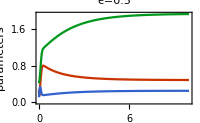

```mathematica
Block[{Ν=64,ϵ=0.5,t1=10,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==RandomReal[],b[0]==ϵ RandomReal[],c[0]==RandomReal[],d[0]==RandomReal[]/ϵ,e[0]==RandomReal[]/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
Plot[{b[t],d[t],e[t]},{t,0,t1},PlotStyle->{Red,Green,Blue},FrameLabel->{"\!\(t\)","parameters"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\)"}),ImageSize->200]]
```

There is a (mean-field) phase transition between A phase (forgetting) and B phase (following). The transition occurs at N ϵ^2=1. No chaotic behavior observed around the transition.

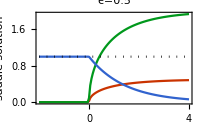

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{b[t1],d[t1],e[t1]^2,b[t1]d[t1]+e[t1]^2}],{lgΝ,0,6,0.05}],
PlotStyle->{Red,Green,Blue,Directive[Dotted,Black]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","saddle solution"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\^2\)","\!\(b d+e\^2\)"}),ImageSize->200]]
```

In the B phase, as N ϵ^2 increases, μ_z gradually grows larger than σ_z, then the consensus is formed.

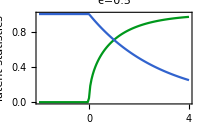

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{d[t1]ϵ,e[t1]}],{lgΝ,0,6,0.05}],
PlotStyle->{Green,Blue},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","latent statistics"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\_z[x]\)","\!\(σ\_z[x]\)"}),ImageSize->200]]
```

To explore the dynamical phase space flow, we reduce the differential equation Eq. (DisplayFormulaNumbered) to two variables b,d, by setting a=c=0 and e^2=1/(N b^2+1)

∂_t b=-(N b)/(N b^2+1)-N ϵ^2 d(b d-1),
∂_t d=- ϵ^2(d-N b (b d-1)),

which can be obtained from the following effective loss function

ℒ=-N ϵ^2 b d+1/2 d^2 ϵ^2(N b^2+1)+log (N b^2+1).

```mathematica
-Collect[D[-Ν ϵ^2 b d+1/2d^2 ϵ^2(Ν b^2+1)+(1/2)Log[Ν b^2+1],#],ϵ,Factor]&/@{b,d}
```

{-d (-1+b d) ϵ^2 Ν-(b Ν)/(1+b^2 Ν),-ϵ^2 (d-b Ν+b^2 d Ν)}

Gradient check.

Flow diagrams under different N ϵ^2.

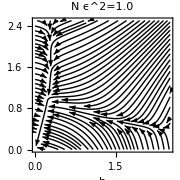
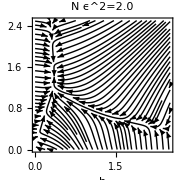
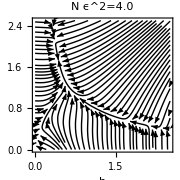

```mathematica
Row@Table[Block[{ϵ=0.5},
StreamPlot[{-Ν b/(Ν b^2+1)-Ν ϵ^2d(b d-1),-ϵ^2(d+Ν b(b d-1))},{b,0,2.5},{d,0,2.5},PlotRangePadding->Scaled[.02],FrameLabel->{"\!\(b\)","\!\(d\)"},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][Ν ϵ^2],StreamScale->Full,StreamPoints->Fine,StreamStyle->Directive[Black,AbsoluteThickness[1]],ImageSize->180]],{Ν,{4,8,16}}]
```

Details near the transition.

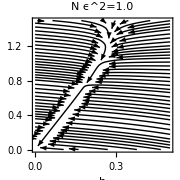
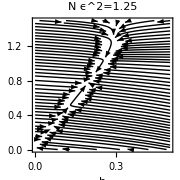

```mathematica
Row@Table[Block[{ϵ=0.5},
StreamPlot[{-Ν b/(Ν b^2+1)-Ν ϵ^2d(b d-1),-ϵ^2(d+Ν b(b d-1))},{b,0,0.5},{d,0,1.5},PlotRangePadding->Scaled[.02],FrameLabel->{"\!\(b\)","\!\(d\)"},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][Ν ϵ^2],StreamScale->Full,StreamPoints->Fine,StreamStyle->Directive[Black,AbsoluteThickness[1]],ImageSize->180]],{Ν,{4,5}}]
```

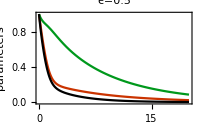

```mathematica
Block[{Ν=2,ϵ=0.5,t1=20,a,b,c,d,e},
{b,d}=NDSolveValue[{
b'[t]==-Ν b[t]/(Ν b[t]^2+1)-Ν ϵ^2d[t](b[t]d[t]-1),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
b[0]==1,d[0]==1},{b,d},{t,0,t1}];
Plot[{b[t],d[t],b[t] d[t]},{t,0,t1},PlotStyle->{Red,Green,Black},FrameLabel->{"\!\(t\)","parameters"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(b d\)"}),ImageSize->200]]
```

#### Cross Over Behavior

The above toy model is a little careless about the variance of x̄ in Eq. (DisplayFormulaNumbered). In fact, according to Eq. (DisplayFormulaNumbered), the variance actually goes like

∫ⅆ x̄ (x̄)^2 p(x̄)=ϵ^2+1/N.

In this case, we need to modify our differential equation to

∂_t a=-N(a+b c),
∂_t b=-N(a c+b (c^2+e^2))-(N ϵ^2+1)d(b d-1),
∂_t c=-(c+N b (a+b c)),
∂_t d=- (ϵ^2+1/N)(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

With this modification, the transition is gone. We can only observe a crossover behavior. In this case b=ϵ remains a constant (meaning that m(z)=ϵ z can learn about the weak measurement strength, even if the machine has no idea of the state yet).

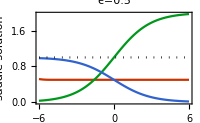

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν (ϵ^2+1/Ν)d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-(ϵ^2+1/Ν)(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{b[t1],d[t1],e[t1]^2,b[t1]d[t1]+e[t1]^2}],{lgΝ,-4,8,0.05}],
PlotStyle->{Red,Green,Blue,Directive[Dotted,Black]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","saddle solution"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\^2\)","\!\(b d+e\^2\)"}),ImageSize->200]]
```

The latent statistics also only have a cross over behavior. The behavior looks quite universal.

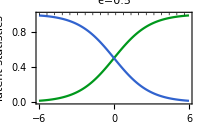

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν (ϵ^2+1/Ν)d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-(ϵ^2+1/Ν)(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{d[t1]ϵ,e[t1]^2,d[t1]ϵ+e[t1]^2}],{lgΝ,-4,8,0.05}],
PlotStyle->{Green,Blue,Directive[Black,Dotted]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","latent statistics"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\_z[x]\)","\!\(σ\_z\%2[x]\)"}),ImageSize->200]]
```

Let us try to understand this universal curve. First we set a=c=0, Eq. (DisplayFormulaNumbered) reduces to

∂_t b=-N b e^2-(N ϵ^2+1)d(b d-1),
∂_t d=- (ϵ^2+1/N)(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

We first solve ∂_t e=0 and find e^2=1/(N b^2+1). Substitute into Eq. (DisplayFormulaNumbered), we obtain

∂_t b=-(N b)/(N b^2+1)-(N ϵ^2+1)d(b d-1),
∂_t d=- (ϵ^2+1/N)(d+N b(b d-1)).

```mathematica
Solve[{Ν b/(Ν b^2+1)+(Ν ϵ^2+1)d(b d-1)==0,(ϵ^2+1/Ν)(d+Ν b(b d-1))==0},{b,d}]
```

{{b→0,d→0},{b→-ϵ,d→-(ϵ Ν)/(1+ϵ^2 Ν)},{b→ϵ,d→(ϵ Ν)/(1+ϵ^2 Ν)}}

Solve.

We find three saddle point solution

A:{ | b=0
d=0, B_±:{ | b=±ϵ
d=±(N ϵ)/(1+N ϵ^2).

Focus on the B_+ solution, it implies

m(z)=ϵ z, μ_z[x]=(N ϵ)/(1+N ϵ^2)x̄, σ_z^2[x]=1/(1+N ϵ^2).

The fidelity-variance sum rule

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z+σ_z^2[x]=1.